# Asymptotic Bounds for the Mertens Function: Maxie D. Schmidt (2017)

## Supplementary Mathematica notebook to check formulas from the article.

## §1: Introduction

The Mathematica code to generate the images in Figure 1.1:

```mathematica
Mertens[alpha_,x_]:=Sum[Power[m,alpha]MoebiusMu[m],{m,1,x}]
```

{-1,0,1,2}

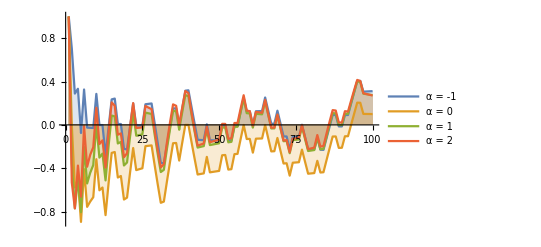

```mathematica
alphas=Range[-1,2,1]
legends=MapIndexed[ToString[StringForm["α = `1`",#1]]&,alphas];
mpoints=Map[Table[{x,Mertens[#1,x]/Power[x,#1+1/2 ]},{x,1,100}]&,alphas];
ListPlot[mpoints,PlotLegends->legends,Joined->True,Filling->Axis]
```

{-1,0,1,2}

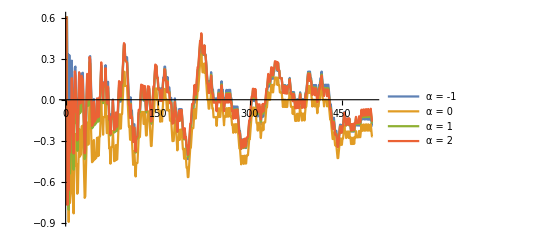

```mathematica
alphas=Range[-1,2,1]
legends=MapIndexed[ToString[StringForm["α = `1`",#1]]&,alphas];
mpoints=Map[Table[{x,Mertens[#1,x]/Power[x,#1+1/2 ]},{x,1,500}]&,alphas];
ListPlot[mpoints,PlotLegends->legends,Joined->True]
```

{-1,0,1,2}

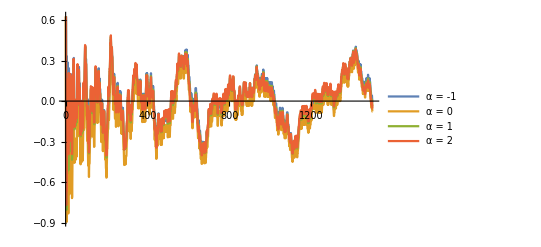

```mathematica
alphas=Range[-1,2,1]
legends=MapIndexed[ToString[StringForm["α = `1`",#1]]&,alphas];
mpoints=Map[Table[{x,Mertens[#1,x]/Power[x,#1 +1/2]},{x,1,1500}]&,alphas];
ListPlot[mpoints,PlotLegends->legends,Joined->True]
```

{-1,0,1,2}

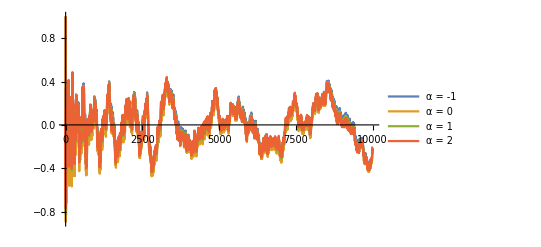

```mathematica
alphas=Range[-1,2,1]
legends=MapIndexed[ToString[StringForm["α = `1`",#1]]&,alphas];
mpoints=Map[Table[{x,Mertens[#1,x]/Power[x,#1+1/2 ]},{x,1,10000}]&,alphas];
ListPlot[mpoints,PlotLegends->legends,Joined->True]
```

Check the Bernoulli polynomial formulas for the negative-order harmonic numbers when t∈Z^+:

```mathematica
Table[diffs[t,n]->FunctionExpand[{HarmonicNumber[n,-t]-(BernoulliB[t+1,n+1]-BernoulliB[t+1])/(t+1),HarmonicNumber[n,-t]-(Power[n,t+1]/(t+1)+Power[n,t]/2+Sum[Binomial[t,k]BernoulliB[k+1]Power[n,t-k]/(k+1),{k,1,t-1}])}],{n,0,35},{t,1,12}] // TableForm
```

diffs[1,0]→{0,0} | diffs[2,0]→{0,0} | diffs[3,0]→{0,0} | diffs[4,0]→{0,0} | diffs[5,0]→{0,0} | diffs[6,0]→{0,0} | diffs[7,0]→{0,0} | diffs[8,0]→{0,0} | diffs[9,0]→{0,0} | diffs[10,0]→{0,0} | diffs[11,0]→{0,0} | diffs[12,0]→{0,0}
diffs[1,1]→{0,0} | diffs[2,1]→{0,0} | diffs[3,1]→{0,0} | diffs[4,1]→{0,0} | diffs[5,1]→{0,0} | diffs[6,1]→{0,0} | diffs[7,1]→{0,0} | diffs[8,1]→{0,0} | diffs[9,1]→{0,0} | diffs[10,1]→{0,0} | diffs[11,1]→{0,0} | diffs[12,1]→{0,0}
diffs[1,2]→{0,0} | diffs[2,2]→{0,0} | diffs[3,2]→{0,0} | diffs[4,2]→{0,0} | diffs[5,2]→{0,0} | diffs[6,2]→{0,0} | diffs[7,2]→{0,0} | diffs[8,2]→{0,0} | diffs[9,2]→{0,0} | diffs[10,2]→{0,0} | diffs[11,2]→{0,0} | diffs[12,2]→{0,0}
diffs[1,3]→{0,0} | diffs[2,3]→{0,0} | diffs[3,3]→{0,0} | diffs[4,3]→{0,0} | diffs[5,3]→{0,0} | diffs[6,3]→{0,0} | diffs[7,3]→{0,0} | diffs[8,3]→{0,0} | diffs[9,3]→{0,0} | diffs[10,3]→{0,0} | diffs[11,3]→{0,0} | diffs[12,3]→{0,0}
diffs[1,4]→{0,0} | diffs[2,4]→{0,0} | diffs[3,4]→{0,0} | diffs[4,4]→{0,0} | diffs[5,4]→{0,0} | diffs[6,4]→{0,0} | diffs[7,4]→{0,0} | diffs[8,4]→{0,0} | diffs[9,4]→{0,0} | diffs[10,4]→{0,0} | diffs[11,4]→{0,0} | diffs[12,4]→{0,0}
diffs[1,5]→{0,0} | diffs[2,5]→{0,0} | diffs[3,5]→{0,0} | diffs[4,5]→{0,0} | diffs[5,5]→{0,0} | diffs[6,5]→{0,0} | diffs[7,5]→{0,0} | diffs[8,5]→{0,0} | diffs[9,5]→{0,0} | diffs[10,5]→{0,0} | diffs[11,5]→{0,0} | diffs[12,5]→{0,0}
diffs[1,6]→{0,0} | diffs[2,6]→{0,0} | diffs[3,6]→{0,0} | diffs[4,6]→{0,0} | diffs[5,6]→{0,0} | diffs[6,6]→{0,0} | diffs[7,6]→{0,0} | diffs[8,6]→{0,0} | diffs[9,6]→{0,0} | diffs[10,6]→{0,0} | diffs[11,6]→{0,0} | diffs[12,6]→{0,0}
diffs[1,7]→{0,0} | diffs[2,7]→{0,0} | diffs[3,7]→{0,0} | diffs[4,7]→{0,0} | diffs[5,7]→{0,0} | diffs[6,7]→{0,0} | diffs[7,7]→{0,0} | diffs[8,7]→{0,0} | diffs[9,7]→{0,0} | diffs[10,7]→{0,0} | diffs[11,7]→{0,0} | diffs[12,7]→{0,0}
diffs[1,8]→{0,0} | diffs[2,8]→{0,0} | diffs[3,8]→{0,0} | diffs[4,8]→{0,0} | diffs[5,8]→{0,0} | diffs[6,8]→{0,0} | diffs[7,8]→{0,0} | diffs[8,8]→{0,0} | diffs[9,8]→{0,0} | diffs[10,8]→{0,0} | diffs[11,8]→{0,0} | diffs[12,8]→{0,0}
diffs[1,9]→{0,0} | diffs[2,9]→{0,0} | diffs[3,9]→{0,0} | diffs[4,9]→{0,0} | diffs[5,9]→{0,0} | diffs[6,9]→{0,0} | diffs[7,9]→{0,0} | diffs[8,9]→{0,0} | diffs[9,9]→{0,0} | diffs[10,9]→{0,0} | diffs[11,9]→{0,0} | diffs[12,9]→{0,0}
diffs[1,10]→{0,0} | diffs[2,10]→{0,0} | diffs[3,10]→{0,0} | diffs[4,10]→{0,0} | diffs[5,10]→{0,0} | diffs[6,10]→{0,0} | diffs[7,10]→{0,0} | diffs[8,10]→{0,0} | diffs[9,10]→{0,0} | diffs[10,10]→{0,0} | diffs[11,10]→{0,0} | diffs[12,10]→{0,0}
diffs[1,11]→{0,0} | diffs[2,11]→{0,0} | diffs[3,11]→{0,0} | diffs[4,11]→{0,0} | diffs[5,11]→{0,0} | diffs[6,11]→{0,0} | diffs[7,11]→{0,0} | diffs[8,11]→{0,0} | diffs[9,11]→{0,0} | diffs[10,11]→{0,0} | diffs[11,11]→{0,0} | diffs[12,11]→{0,0}
diffs[1,12]→{0,0} | diffs[2,12]→{0,0} | diffs[3,12]→{0,0} | diffs[4,12]→{0,0} | diffs[5,12]→{0,0} | diffs[6,12]→{0,0} | diffs[7,12]→{0,0} | diffs[8,12]→{0,0} | diffs[9,12]→{0,0} | diffs[10,12]→{0,0} | diffs[11,12]→{0,0} | diffs[12,12]→{0,0}
diffs[1,13]→{0,0} | diffs[2,13]→{0,0} | diffs[3,13]→{0,0} | diffs[4,13]→{0,0} | diffs[5,13]→{0,0} | diffs[6,13]→{0,0} | diffs[7,13]→{0,0} | diffs[8,13]→{0,0} | diffs[9,13]→{0,0} | diffs[10,13]→{0,0} | diffs[11,13]→{0,0} | diffs[12,13]→{0,0}
diffs[1,14]→{0,0} | diffs[2,14]→{0,0} | diffs[3,14]→{0,0} | diffs[4,14]→{0,0} | diffs[5,14]→{0,0} | diffs[6,14]→{0,0} | diffs[7,14]→{0,0} | diffs[8,14]→{0,0} | diffs[9,14]→{0,0} | diffs[10,14]→{0,0} | diffs[11,14]→{0,0} | diffs[12,14]→{0,0}
diffs[1,15]→{0,0} | diffs[2,15]→{0,0} | diffs[3,15]→{0,0} | diffs[4,15]→{0,0} | diffs[5,15]→{0,0} | diffs[6,15]→{0,0} | diffs[7,15]→{0,0} | diffs[8,15]→{0,0} | diffs[9,15]→{0,0} | diffs[10,15]→{0,0} | diffs[11,15]→{0,0} | diffs[12,15]→{0,0}
diffs[1,16]→{0,0} | diffs[2,16]→{0,0} | diffs[3,16]→{0,0} | diffs[4,16]→{0,0} | diffs[5,16]→{0,0} | diffs[6,16]→{0,0} | diffs[7,16]→{0,0} | diffs[8,16]→{0,0} | diffs[9,16]→{0,0} | diffs[10,16]→{0,0} | diffs[11,16]→{0,0} | diffs[12,16]→{0,0}
diffs[1,17]→{0,0} | diffs[2,17]→{0,0} | diffs[3,17]→{0,0} | diffs[4,17]→{0,0} | diffs[5,17]→{0,0} | diffs[6,17]→{0,0} | diffs[7,17]→{0,0} | diffs[8,17]→{0,0} | diffs[9,17]→{0,0} | diffs[10,17]→{0,0} | diffs[11,17]→{0,0} | diffs[12,17]→{0,0}
diffs[1,18]→{0,0} | diffs[2,18]→{0,0} | diffs[3,18]→{0,0} | diffs[4,18]→{0,0} | diffs[5,18]→{0,0} | diffs[6,18]→{0,0} | diffs[7,18]→{0,0} | diffs[8,18]→{0,0} | diffs[9,18]→{0,0} | diffs[10,18]→{0,0} | diffs[11,18]→{0,0} | diffs[12,18]→{0,0}
diffs[1,19]→{0,0} | diffs[2,19]→{0,0} | diffs[3,19]→{0,0} | diffs[4,19]→{0,0} | diffs[5,19]→{0,0} | diffs[6,19]→{0,0} | diffs[7,19]→{0,0} | diffs[8,19]→{0,0} | diffs[9,19]→{0,0} | diffs[10,19]→{0,0} | diffs[11,19]→{0,0} | diffs[12,19]→{0,0}
diffs[1,20]→{0,0} | diffs[2,20]→{0,0} | diffs[3,20]→{0,0} | diffs[4,20]→{0,0} | diffs[5,20]→{0,0} | diffs[6,20]→{0,0} | diffs[7,20]→{0,0} | diffs[8,20]→{0,0} | diffs[9,20]→{0,0} | diffs[10,20]→{0,0} | diffs[11,20]→{0,0} | diffs[12,20]→{0,0}
diffs[1,21]→{0,0} | diffs[2,21]→{0,0} | diffs[3,21]→{0,0} | diffs[4,21]→{0,0} | diffs[5,21]→{0,0} | diffs[6,21]→{0,0} | diffs[7,21]→{0,0} | diffs[8,21]→{0,0} | diffs[9,21]→{0,0} | diffs[10,21]→{0,0} | diffs[11,21]→{0,0} | diffs[12,21]→{0,0}
diffs[1,22]→{0,0} | diffs[2,22]→{0,0} | diffs[3,22]→{0,0} | diffs[4,22]→{0,0} | diffs[5,22]→{0,0} | diffs[6,22]→{0,0} | diffs[7,22]→{0,0} | diffs[8,22]→{0,0} | diffs[9,22]→{0,0} | diffs[10,22]→{0,0} | diffs[11,22]→{0,0} | diffs[12,22]→{0,0}
diffs[1,23]→{0,0} | diffs[2,23]→{0,0} | diffs[3,23]→{0,0} | diffs[4,23]→{0,0} | diffs[5,23]→{0,0} | diffs[6,23]→{0,0} | diffs[7,23]→{0,0} | diffs[8,23]→{0,0} | diffs[9,23]→{0,0} | diffs[10,23]→{0,0} | diffs[11,23]→{0,0} | diffs[12,23]→{0,0}
diffs[1,24]→{0,0} | diffs[2,24]→{0,0} | diffs[3,24]→{0,0} | diffs[4,24]→{0,0} | diffs[5,24]→{0,0} | diffs[6,24]→{0,0} | diffs[7,24]→{0,0} | diffs[8,24]→{0,0} | diffs[9,24]→{0,0} | diffs[10,24]→{0,0} | diffs[11,24]→{0,0} | diffs[12,24]→{0,0}
diffs[1,25]→{0,0} | diffs[2,25]→{0,0} | diffs[3,25]→{0,0} | diffs[4,25]→{0,0} | diffs[5,25]→{0,0} | diffs[6,25]→{0,0} | diffs[7,25]→{0,0} | diffs[8,25]→{0,0} | diffs[9,25]→{0,0} | diffs[10,25]→{0,0} | diffs[11,25]→{0,0} | diffs[12,25]→{0,0}
diffs[1,26]→{0,0} | diffs[2,26]→{0,0} | diffs[3,26]→{0,0} | diffs[4,26]→{0,0} | diffs[5,26]→{0,0} | diffs[6,26]→{0,0} | diffs[7,26]→{0,0} | diffs[8,26]→{0,0} | diffs[9,26]→{0,0} | diffs[10,26]→{0,0} | diffs[11,26]→{0,0} | diffs[12,26]→{0,0}
diffs[1,27]→{0,0} | diffs[2,27]→{0,0} | diffs[3,27]→{0,0} | diffs[4,27]→{0,0} | diffs[5,27]→{0,0} | diffs[6,27]→{0,0} | diffs[7,27]→{0,0} | diffs[8,27]→{0,0} | diffs[9,27]→{0,0} | diffs[10,27]→{0,0} | diffs[11,27]→{0,0} | diffs[12,27]→{0,0}
diffs[1,28]→{0,0} | diffs[2,28]→{0,0} | diffs[3,28]→{0,0} | diffs[4,28]→{0,0} | diffs[5,28]→{0,0} | diffs[6,28]→{0,0} | diffs[7,28]→{0,0} | diffs[8,28]→{0,0} | diffs[9,28]→{0,0} | diffs[10,28]→{0,0} | diffs[11,28]→{0,0} | diffs[12,28]→{0,0}
diffs[1,29]→{0,0} | diffs[2,29]→{0,0} | diffs[3,29]→{0,0} | diffs[4,29]→{0,0} | diffs[5,29]→{0,0} | diffs[6,29]→{0,0} | diffs[7,29]→{0,0} | diffs[8,29]→{0,0} | diffs[9,29]→{0,0} | diffs[10,29]→{0,0} | diffs[11,29]→{0,0} | diffs[12,29]→{0,0}
diffs[1,30]→{0,0} | diffs[2,30]→{0,0} | diffs[3,30]→{0,0} | diffs[4,30]→{0,0} | diffs[5,30]→{0,0} | diffs[6,30]→{0,0} | diffs[7,30]→{0,0} | diffs[8,30]→{0,0} | diffs[9,30]→{0,0} | diffs[10,30]→{0,0} | diffs[11,30]→{0,0} | diffs[12,30]→{0,0}
diffs[1,31]→{0,0} | diffs[2,31]→{0,0} | diffs[3,31]→{0,0} | diffs[4,31]→{0,0} | diffs[5,31]→{0,0} | diffs[6,31]→{0,0} | diffs[7,31]→{0,0} | diffs[8,31]→{0,0} | diffs[9,31]→{0,0} | diffs[10,31]→{0,0} | diffs[11,31]→{0,0} | diffs[12,31]→{0,0}
diffs[1,32]→{0,0} | diffs[2,32]→{0,0} | diffs[3,32]→{0,0} | diffs[4,32]→{0,0} | diffs[5,32]→{0,0} | diffs[6,32]→{0,0} | diffs[7,32]→{0,0} | diffs[8,32]→{0,0} | diffs[9,32]→{0,0} | diffs[10,32]→{0,0} | diffs[11,32]→{0,0} | diffs[12,32]→{0,0}
diffs[1,33]→{0,0} | diffs[2,33]→{0,0} | diffs[3,33]→{0,0} | diffs[4,33]→{0,0} | diffs[5,33]→{0,0} | diffs[6,33]→{0,0} | diffs[7,33]→{0,0} | diffs[8,33]→{0,0} | diffs[9,33]→{0,0} | diffs[10,33]→{0,0} | diffs[11,33]→{0,0} | diffs[12,33]→{0,0}
diffs[1,34]→{0,0} | diffs[2,34]→{0,0} | diffs[3,34]→{0,0} | diffs[4,34]→{0,0} | diffs[5,34]→{0,0} | diffs[6,34]→{0,0} | diffs[7,34]→{0,0} | diffs[8,34]→{0,0} | diffs[9,34]→{0,0} | diffs[10,34]→{0,0} | diffs[11,34]→{0,0} | diffs[12,34]→{0,0}
diffs[1,35]→{0,0} | diffs[2,35]→{0,0} | diffs[3,35]→{0,0} | diffs[4,35]→{0,0} | diffs[5,35]→{0,0} | diffs[6,35]→{0,0} | diffs[7,35]→{0,0} | diffs[8,35]→{0,0} | diffs[9,35]→{0,0} | diffs[10,35]→{0,0} | diffs[11,35]→{0,0} | diffs[12,35]→{0,0}

Check the formulas for the generalized sum-of-divisors functions stated in Theorem 1.1 and in the restatement provided below:

```mathematica
eps[p_,n_]:=With[{pexp=Select[FactorInteger[n],#[[1]]==p&]},If[pexp≠{},pexp[[1]][[2]],0]]
PI[x_]:=If[PrimeQ[x],1,0]
NotPI[x_]:=If[PrimeQ[x],0,1]
ModQ[x_,a_,mod_]:=If[MemberQ[a,Mod[x,mod,0]],1,0]
Mertens[alpha_,x_]:=Sum[Power[m,alpha]MoebiusMu[m],{m,1,x}]
HarmonicNumberSequence[n_,r_]:=If[n<0,0,HarmonicNumber[n,r]]
SetS[i_,x_]:=Select[Range[12,x],Divisible[#,i]&&(eps[2,#]≥2||EvenQ[#]&&PrimeNu[#]≥3||OddQ[#])&&(MoebiusMu[#/i]≠0)&&If[IntegerQ[Log[2,#]],#/i>2,True]&&!PrimeQ[#]&]
MProduct[n_]:=DivisorSum[n,-#/(q^#-1)*MoebiusMu[n/#]&]
TauDivisorSum[alpha_,x_]:=SeriesCoefficient[Sum[DivisorSum[k,MProduct,!PrimePowerQ[#]&&!PrimePowerQ[#/2]&]/Power[k,1-alpha],{k,1,x}],{q,0,x}]
S1[alpha_,x_]:=Sum[PI[p](p^(alpha*k))HarmonicNumberSequence[Floor[x/(p^k)],1-alpha](Floor[x/(p^k)]-Floor[x/(p^k)-1/p]-1/p),{p,2,x},{k,1,eps[p,x]+1}]
S2[alpha_,x_]:=Sum[PI[p]Power[2,alpha-1]Power[p,alpha*k]Power[-1,Floor[x/Power[p,k-1]]]HarmonicNumberSequence[Floor[x/2/Power[p,k]],1-alpha](Floor[x/Power[p,k]]-Floor[x/Power[p,k]-1/p]-1/p),{p,3,x},{k,1,eps[p,x]+1}]
DivisorSigmaFormula[alpha_,x_]:=FunctionExpand[(HarmonicNumberSequence[x,1-alpha]+TauDivisorSum[alpha,x]+S1[alpha,x]+S2[alpha,x])]
```

```mathematica
Table[idx[x]->{FullSimplify[Expand[DivisorSigmaFormula[α,x]-DivisorSigma[α,x]]],Expand[FullSimplify[DivisorSigma[α,x]]]},{x,1,25}] // TableForm
```

idx[1]→{0,1}
idx[2]→{0,1+2^α}
idx[3]→{0,1+3^α}
idx[4]→{0,1+2^α+4^α}
idx[5]→{0,1+5^α}
idx[6]→{0,1+2^α+3^α+6^α}
idx[7]→{0,1+7^α}
idx[8]→{0,1+2^α+4^α+8^α}
idx[9]→{0,1+3^α+9^α}
idx[10]→{0,1+2^α+5^α+10^α}
idx[11]→{0,1+11^α}
idx[12]→{0,1+2^α+3^α+4^α+6^α+12^α}
idx[13]→{0,1+13^α}
idx[14]→{0,1+2^α+7^α+14^α}
idx[15]→{0,1+3^α+5^α+15^α}
idx[16]→{0,1+2^α+4^α+8^α+16^α}
idx[17]→{0,1+17^α}
idx[18]→{0,1+2^α+3^α+6^α+9^α+18^α}
idx[19]→{0,1+19^α}
idx[20]→{0,1+2^α+4^α+5^α+10^α+20^α}
idx[21]→{0,1+3^α+7^α+21^α}
idx[22]→{0,1+2^α+11^α+22^α}
idx[23]→{0,1+23^α}
idx[24]→{0,1+2^α+3^α+4^α+6^α+8^α+12^α+24^α}
idx[25]→{0,1+5^α+25^α}

## §2.1: Statement of the main theorem

Historical perspective:

```mathematica
Reduce[1/10*Log[Log[x*Log[x]-1]]-Log[Log[Log[x*Log[x]]]]>1,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[1/10 Log[Log[-1+x Log[x]]]-Log[Log[Log[x Log[x]]]]>1,x]

```mathematica
Reduce[1/10*Log[Log[x*Log[x]-1]]-Log[Log[Log[x*Log[x]]]]==1,x]
```

```mathematica
FindInstance[1/10*Log[Log[x*Log[x]-1]]-Log[Log[Log[x*Log[x]]]]==1,x,Reals,2]
N[%]
```

$Aborted

$Aborted

## §2.2: Key asymptotic bounds and formulas

The formulas for the divisor sums in Lemma 2.4:

```mathematica
SetS[i_,x_]:=Select[Range[12,x],!PrimePowerQ[#]&&!PrimePowerQ[#/2]&]
SetS[x_]:=Union[Flatten[Map[SetS[#1,#1]&,Range[12,x]]]]

MProduct[n_]:=DivisorSum[n,-#/(q^#-1)*MoebiusMu[n/#]&]
TauDivisorSum[alpha_,x_]:=SeriesCoefficient[Sum[DivisorSum[k,MProduct,!PrimePowerQ[#]&&!PrimePowerQ[#/2]&]/Power[k,-alpha],{k,1,x}],{q,0,x}]

innerSum2[alpha_,r_,x_]:=Sum[DivisorSum[k,r*MoebiusMu[#/r](k^(alpha))If[Divisible[GCD[#,x],r],1,0]&,!PrimePowerQ[#]&&!PrimePowerQ[#/2]&],{k,1,x}]
TauDivisorSum2[alpha_,x_]:=DivisorSum[x,innerSum2[alpha,#,x]&]

ChiPP[x_]:=If[!PrimePowerQ[x]&&!PrimePowerQ[x/2],1,0]

innerSum7[alpha_,d_,x_,m_]:=DivisorSum[GCD[d,x],Power[#,alpha+1]&,m==d/#&]
d7[alpha_,x_,m_]:=Sum[DivisorSum[k,innerSum7[alpha,#,x,m]Power[k/#,alpha]ChiPP[#]&],{k,1,x}]
TauDivisorSum7[alpha_,x_]:=Sum[MoebiusMu[m]Power[m,alpha]*d7[alpha,x,m],{m,1,x}]

innerSumTv[alpha_,d_,x_]:=DivisorSum[GCD[d,x],# MoebiusMu[d/#]&]
Tv[alpha_,x_]:=Sum[DivisorSum[k,innerSumTv[alpha,#,x]Power[k,alpha]ChiPP[#]&,#<Floor[(x-1)Exp[-1/Sqrt[x]]]&],{k,1,x}]
innerSumd[alpha_,d_,x_,m_]:=DivisorSum[GCD[d,x],Power[#,alpha+1]&,m==d/#&]
d[alpha_,x_,m_]:=Sum[DivisorSum[k,innerSumd[alpha,#,x,m]Power[k/#,alpha]ChiPP[#]&,#≥Floor[(x-1)Exp[-1/Sqrt[x]]]&],{k,1,x}]
TauDivisorSumd[alpha_,x_]:=Sum[MoebiusMu[m]Power[m,alpha]*d[alpha,x,m],{m,1,x}]
TauDivisorSum8[alpha_,x_]:=Tv[alpha,x]+TauDivisorSumd[alpha,x]
```

```mathematica
Table[diffs[alpha,x]->FS[{TauDivisorSum[a,x]-TauDivisorSum2[a,x],TauDivisorSum[a,x]-TauDivisorSum7[a,x],TauDivisorSum[a,x]-TauDivisorSum8[a,x]}],{x,12,42},{a,0,6}] // TableForm
```

diffs[alpha,12]→{0,0,0} | diffs[alpha,12]→{0,0,0} | diffs[alpha,12]→{0,0,0} | diffs[alpha,12]→{0,0,0} | diffs[alpha,12]→{0,0,0} | diffs[alpha,12]→{0,0,0} | diffs[alpha,12]→{0,0,0}
diffs[alpha,13]→{0,0,0} | diffs[alpha,13]→{0,0,0} | diffs[alpha,13]→{0,0,0} | diffs[alpha,13]→{0,0,0} | diffs[alpha,13]→{0,0,0} | diffs[alpha,13]→{0,0,0} | diffs[alpha,13]→{0,0,0}
diffs[alpha,14]→{0,0,0} | diffs[alpha,14]→{0,0,0} | diffs[alpha,14]→{0,0,0} | diffs[alpha,14]→{0,0,0} | diffs[alpha,14]→{0,0,0} | diffs[alpha,14]→{0,0,0} | diffs[alpha,14]→{0,0,0}
diffs[alpha,15]→{0,0,0} | diffs[alpha,15]→{0,0,0} | diffs[alpha,15]→{0,0,0} | diffs[alpha,15]→{0,0,0} | diffs[alpha,15]→{0,0,0} | diffs[alpha,15]→{0,0,0} | diffs[alpha,15]→{0,0,0}
diffs[alpha,16]→{0,0,0} | diffs[alpha,16]→{0,0,0} | diffs[alpha,16]→{0,0,0} | diffs[alpha,16]→{0,0,0} | diffs[alpha,16]→{0,0,0} | diffs[alpha,16]→{0,0,0} | diffs[alpha,16]→{0,0,0}
diffs[alpha,17]→{0,0,0} | diffs[alpha,17]→{0,0,0} | diffs[alpha,17]→{0,0,0} | diffs[alpha,17]→{0,0,0} | diffs[alpha,17]→{0,0,0} | diffs[alpha,17]→{0,0,0} | diffs[alpha,17]→{0,0,0}
diffs[alpha,18]→{0,0,0} | diffs[alpha,18]→{0,0,0} | diffs[alpha,18]→{0,0,0} | diffs[alpha,18]→{0,0,0} | diffs[alpha,18]→{0,0,0} | diffs[alpha,18]→{0,0,0} | diffs[alpha,18]→{0,0,0}
diffs[alpha,19]→{0,0,0} | diffs[alpha,19]→{0,0,0} | diffs[alpha,19]→{0,0,0} | diffs[alpha,19]→{0,0,0} | diffs[alpha,19]→{0,0,0} | diffs[alpha,19]→{0,0,0} | diffs[alpha,19]→{0,0,0}
diffs[alpha,20]→{0,0,0} | diffs[alpha,20]→{0,0,0} | diffs[alpha,20]→{0,0,0} | diffs[alpha,20]→{0,0,0} | diffs[alpha,20]→{0,0,0} | diffs[alpha,20]→{0,0,0} | diffs[alpha,20]→{0,0,0}
diffs[alpha,21]→{0,0,0} | diffs[alpha,21]→{0,0,0} | diffs[alpha,21]→{0,0,0} | diffs[alpha,21]→{0,0,0} | diffs[alpha,21]→{0,0,0} | diffs[alpha,21]→{0,0,0} | diffs[alpha,21]→{0,0,0}
diffs[alpha,22]→{0,0,0} | diffs[alpha,22]→{0,0,0} | diffs[alpha,22]→{0,0,0} | diffs[alpha,22]→{0,0,0} | diffs[alpha,22]→{0,0,0} | diffs[alpha,22]→{0,0,0} | diffs[alpha,22]→{0,0,0}
diffs[alpha,23]→{0,0,0} | diffs[alpha,23]→{0,0,0} | diffs[alpha,23]→{0,0,0} | diffs[alpha,23]→{0,0,0} | diffs[alpha,23]→{0,0,0} | diffs[alpha,23]→{0,0,0} | diffs[alpha,23]→{0,0,0}
diffs[alpha,24]→{0,0,0} | diffs[alpha,24]→{0,0,0} | diffs[alpha,24]→{0,0,0} | diffs[alpha,24]→{0,0,0} | diffs[alpha,24]→{0,0,0} | diffs[alpha,24]→{0,0,0} | diffs[alpha,24]→{0,0,0}
diffs[alpha,25]→{0,0,0} | diffs[alpha,25]→{0,0,0} | diffs[alpha,25]→{0,0,0} | diffs[alpha,25]→{0,0,0} | diffs[alpha,25]→{0,0,0} | diffs[alpha,25]→{0,0,0} | diffs[alpha,25]→{0,0,0}
diffs[alpha,26]→{0,0,0} | diffs[alpha,26]→{0,0,0} | diffs[alpha,26]→{0,0,0} | diffs[alpha,26]→{0,0,0} | diffs[alpha,26]→{0,0,0} | diffs[alpha,26]→{0,0,0} | diffs[alpha,26]→{0,0,0}
diffs[alpha,27]→{0,0,0} | diffs[alpha,27]→{0,0,0} | diffs[alpha,27]→{0,0,0} | diffs[alpha,27]→{0,0,0} | diffs[alpha,27]→{0,0,0} | diffs[alpha,27]→{0,0,0} | diffs[alpha,27]→{0,0,0}
diffs[alpha,28]→{0,0,0} | diffs[alpha,28]→{0,0,0} | diffs[alpha,28]→{0,0,0} | diffs[alpha,28]→{0,0,0} | diffs[alpha,28]→{0,0,0} | diffs[alpha,28]→{0,0,0} | diffs[alpha,28]→{0,0,0}
diffs[alpha,29]→{0,0,0} | diffs[alpha,29]→{0,0,0} | diffs[alpha,29]→{0,0,0} | diffs[alpha,29]→{0,0,0} | diffs[alpha,29]→{0,0,0} | diffs[alpha,29]→{0,0,0} | diffs[alpha,29]→{0,0,0}
diffs[alpha,30]→{0,0,0} | diffs[alpha,30]→{0,0,0} | diffs[alpha,30]→{0,0,0} | diffs[alpha,30]→{0,0,0} | diffs[alpha,30]→{0,0,0} | diffs[alpha,30]→{0,0,0} | diffs[alpha,30]→{0,0,0}
diffs[alpha,31]→{0,0,0} | diffs[alpha,31]→{0,0,0} | diffs[alpha,31]→{0,0,0} | diffs[alpha,31]→{0,0,0} | diffs[alpha,31]→{0,0,0} | diffs[alpha,31]→{0,0,0} | diffs[alpha,31]→{0,0,0}
diffs[alpha,32]→{0,0,0} | diffs[alpha,32]→{0,0,0} | diffs[alpha,32]→{0,0,0} | diffs[alpha,32]→{0,0,0} | diffs[alpha,32]→{0,0,0} | diffs[alpha,32]→{0,0,0} | diffs[alpha,32]→{0,0,0}
diffs[alpha,33]→{0,0,0} | diffs[alpha,33]→{0,0,0} | diffs[alpha,33]→{0,0,0} | diffs[alpha,33]→{0,0,0} | diffs[alpha,33]→{0,0,0} | diffs[alpha,33]→{0,0,0} | diffs[alpha,33]→{0,0,0}
diffs[alpha,34]→{0,0,0} | diffs[alpha,34]→{0,0,0} | diffs[alpha,34]→{0,0,0} | diffs[alpha,34]→{0,0,0} | diffs[alpha,34]→{0,0,0} | diffs[alpha,34]→{0,0,0} | diffs[alpha,34]→{0,0,0}
diffs[alpha,35]→{0,0,0} | diffs[alpha,35]→{0,0,0} | diffs[alpha,35]→{0,0,0} | diffs[alpha,35]→{0,0,0} | diffs[alpha,35]→{0,0,0} | diffs[alpha,35]→{0,0,0} | diffs[alpha,35]→{0,0,0}
diffs[alpha,36]→{0,0,0} | diffs[alpha,36]→{0,0,0} | diffs[alpha,36]→{0,0,0} | diffs[alpha,36]→{0,0,0} | diffs[alpha,36]→{0,0,0} | diffs[alpha,36]→{0,0,0} | diffs[alpha,36]→{0,0,0}
diffs[alpha,37]→{0,0,0} | diffs[alpha,37]→{0,0,0} | diffs[alpha,37]→{0,0,0} | diffs[alpha,37]→{0,0,0} | diffs[alpha,37]→{0,0,0} | diffs[alpha,37]→{0,0,0} | diffs[alpha,37]→{0,0,0}
diffs[alpha,38]→{0,0,0} | diffs[alpha,38]→{0,0,0} | diffs[alpha,38]→{0,0,0} | diffs[alpha,38]→{0,0,0} | diffs[alpha,38]→{0,0,0} | diffs[alpha,38]→{0,0,0} | diffs[alpha,38]→{0,0,0}
diffs[alpha,39]→{0,0,0} | diffs[alpha,39]→{0,0,0} | diffs[alpha,39]→{0,0,0} | diffs[alpha,39]→{0,0,0} | diffs[alpha,39]→{0,0,0} | diffs[alpha,39]→{0,0,0} | diffs[alpha,39]→{0,0,0}
diffs[alpha,40]→{0,0,0} | diffs[alpha,40]→{0,0,0} | diffs[alpha,40]→{0,0,0} | diffs[alpha,40]→{0,0,0} | diffs[alpha,40]→{0,0,0} | diffs[alpha,40]→{0,0,0} | diffs[alpha,40]→{0,0,0}
diffs[alpha,41]→{0,0,0} | diffs[alpha,41]→{0,0,0} | diffs[alpha,41]→{0,0,0} | diffs[alpha,41]→{0,0,0} | diffs[alpha,41]→{0,0,0} | diffs[alpha,41]→{0,0,0} | diffs[alpha,41]→{0,0,0}
diffs[alpha,42]→{0,0,0} | diffs[alpha,42]→{0,0,0} | diffs[alpha,42]→{0,0,0} | diffs[alpha,42]→{0,0,0} | diffs[alpha,42]→{0,0,0} | diffs[alpha,42]→{0,0,0} | diffs[alpha,42]→{0,0,0}

Connection to Ramanujan’s sum:

```mathematica
Table[diffs[alpha,x]->FS[{TauDivisorSum[0,x]-Sum[DivisorSum[k,ChiPP[#]MoebiusMu[#/GCD[#,x]]EulerPhi[#]/EulerPhi[#/GCD[#,x]]&],{k,1,x}]}],{x,12,42}] // TableForm
```

diffs[alpha,12]→{0}
diffs[alpha,13]→{0}
diffs[alpha,14]→{0}
diffs[alpha,15]→{0}
diffs[alpha,16]→{0}
diffs[alpha,17]→{0}
diffs[alpha,18]→{0}
diffs[alpha,19]→{0}
diffs[alpha,20]→{0}
diffs[alpha,21]→{0}
diffs[alpha,22]→{0}
diffs[alpha,23]→{0}
diffs[alpha,24]→{0}
diffs[alpha,25]→{0}
diffs[alpha,26]→{0}
diffs[alpha,27]→{0}
diffs[alpha,28]→{0}
diffs[alpha,29]→{0}
diffs[alpha,30]→{0}
diffs[alpha,31]→{0}
diffs[alpha,32]→{0}
diffs[alpha,33]→{0}
diffs[alpha,34]→{0}
diffs[alpha,35]→{0}
diffs[alpha,36]→{0}
diffs[alpha,37]→{0}
diffs[alpha,38]→{0}
diffs[alpha,39]→{0}
diffs[alpha,40]→{0}
diffs[alpha,41]→{0}
diffs[alpha,42]→{0}

Lemma 2.6:

```mathematica
Dv[alpha_,x_]:=Sum[Abs[d[alpha,x,m]],{m,1,x}]
innerDvSum2[alpha_,d_,x_]:=DivisorSum[GCD[d,x],Power[#,alpha+1]&]
DvSum2[alpha_,x_]:=Sum[DivisorSum[k,innerDvSum2[alpha,#,x]Power[k/#,alpha]ChiPP[#]&,#≥Floor[(x-1)Exp[-1/Sqrt[x]]]&],{k,1,x}]
SupRHS[x_]:=Max[Table[Abs[Mertens[0,i]],{i,1,x}]]
LHSFormula[x_]:=(Abs[TauDivisorSum[0,x]]-Abs[Tv[0,x]]+d[0,x,1])/(2*Dv[0,x])-1/2
```

```mathematica
Table[{Idx->x,Dv[0,x],DvSum2[0,x]},{x,1,25}] // TF
```

Idx→1 | 0 | 0
Idx→2 | 0 | 0
Idx→3 | 0 | 0
Idx→4 | 0 | 0
Idx→5 | 0 | 0
Idx→6 | 0 | 0
Idx→7 | 0 | 0
Idx→8 | 0 | 0
Idx→9 | 0 | 0
Idx→10 | 0 | 0
Idx→11 | 0 | 0
Idx→12 | 28 | 28
Idx→13 | 1 | 1
Idx→14 | 3 | 3
Idx→15 | 28 | 28
Idx→16 | 8 | 8
Idx→17 | 2 | 2
Idx→18 | 4 | 4
Idx→19 | 1 | 1
Idx→20 | 48 | 48
Idx→21 | 33 | 33
Idx→22 | 4 | 4
Idx→23 | 2 | 2
Idx→24 | 71 | 71
Idx→25 | 8 | 8

```mathematica
Table[{Idx->x,LHSFormula[x],SupRHS[x]},{x,Table[Prime[m],{m,6,50}]}] // TF
```

Idx→13 | -1/2 | 3
Idx→17 | -1/4 | 3
Idx→19 | 0 | 3
Idx→23 | -1/4 | 3
Idx→29 | -1/2 | 3
Idx→31 | -3/4 | 4
Idx→37 | -3/8 | 4
Idx→41 | -1/4 | 4
Idx→43 | -1/2 | 4
Idx→47 | -1/2 | 4
Idx→53 | -3/8 | 4
Idx→59 | -1/5 | 4
Idx→61 | -3/10 | 4
Idx→67 | -1/2 | 4
Idx→71 | -1/2 | 4
Idx→73 | -1/2 | 4
Idx→79 | -1/2 | 4
Idx→83 | -1/2 | 4
Idx→89 | -3/10 | 4
Idx→97 | -1/4 | 4
Idx→101 | -5/16 | 4
Idx→103 | -3/7 | 4
Idx→107 | -2/3 | 4
Idx→109 | -2/3 | 4
Idx→113 | -9/14 | 5
Idx→127 | -5/16 | 6
Idx→131 | -5/14 | 6
Idx→137 | -7/16 | 6
Idx→139 | -1/2 | 6
Idx→149 | -7/18 | 6
Idx→151 | -7/18 | 6
Idx→157 | -9/20 | 6
Idx→163 | -7/18 | 6
Idx→167 | -4/9 | 6
Idx→173 | -1/2 | 6
Idx→179 | -11/18 | 6
Idx→181 | -5/9 | 6
Idx→191 | -11/24 | 6
Idx→193 | -1/2 | 6
Idx→197 | -13/24 | 7
Idx→199 | -6/11 | 8
Idx→211 | -3/11 | 8
Idx→223 | -7/26 | 8
Idx→227 | -7/22 | 8
Idx→229 | -7/22 | 8

```mathematica
Table[{Idx->x,Abs[TauDivisorSum[0,x]],Abs[Tv[0,x]]+Abs[TauDivisorSumd[0,x]],Abs[Tv[0,x]]+Abs[Mertens[0,x]]d[0,x,x]+Sum[Abs[Mertens[0,x]]Abs[d[0,x,m+1]-d[0,x,m]],{m,1,x-1}],Abs[Tv[0,x]]+2*Sum[Abs[Mertens[0,x]]d[0,x,m],{m,1,x}]+Sum[Abs[MoebiusMu[m]]d[0,x,m],{m,1,x}]-d[0,x,1],Abs[Tv[0,x]]+(2*SupRHS[x]+1)Dv[0,x]-d[0,x,1]},{x,Table[Prime[m],{m,6,25}]}] // TF
```

Idx→13 | 0 | 0 | 6 | 6 | 7
Idx→17 | 1 | 1 | 8 | 9 | 14
Idx→19 | 1 | 1 | 6 | 7 | 7
Idx→23 | 2 | 2 | 5 | 10 | 15
Idx→29 | 2 | 2 | 10 | 10 | 16
Idx→31 | 2 | 4 | 19 | 20 | 21
Idx→37 | 4 | 4 | 15 | 22 | 39
Idx→41 | 5 | 5 | 7 | 13 | 39
Idx→43 | 5 | 5 | 23 | 31 | 41
Idx→47 | 6 | 6 | 24 | 38 | 51
Idx→53 | 7 | 7 | 24 | 31 | 42
Idx→59 | 9 | 9 | 10 | 19 | 51
Idx→61 | 9 | 9 | 19 | 29 | 52
Idx→67 | 11 | 11 | 23 | 29 | 47
Idx→71 | 12 | 12 | 30 | 52 | 66
Idx→73 | 12 | 12 | 36 | 64 | 66
Idx→79 | 14 | 14 | 38 | 74 | 77
Idx→83 | 14 | 14 | 30 | 56 | 59
Idx→89 | 16 | 16 | 26 | 36 | 59
Idx→97 | 19 | 19 | 21 | 35 | 87

Remark 2.7: Generating the cited images:

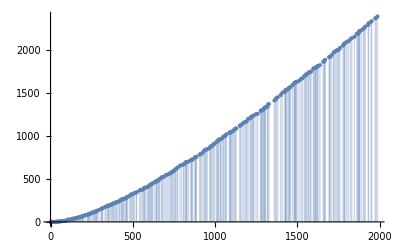

{A→1.,p→1.00833}

```mathematica
Table[{x,Sum[ChiPP[k]DivisorSum[k,inner[#,x]ChiPP[#]&,#>1&&If[PrimeQ[#],#==x,True]&&#<Power[x,0.75]/Log[Log[x]]&],{k,1,x}]},{x,Table[Prime[m],{m,1,300}]}];
ListPlot[%,Filling->Axis]
FindFit[%%,(x^p),{A,p},x]
```

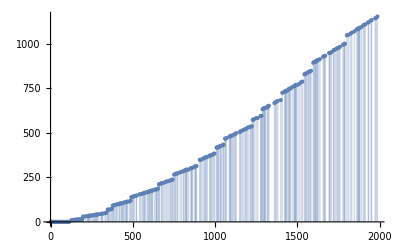

{A→1.,p→0.905158}

```mathematica
Table[{x,Sum[ChiPP[k]DivisorSum[k,inner[#,x]ChiPP[#]&,#>1&&If[PrimeQ[#],#==x,True]&&#<Power[x,0.61]/Log[Log[x]]&],{k,1,x}]},{x,Table[Prime[m],{m,1,300}]}];
ListPlot[%,Filling->Axis]
FindFit[%%,(x^p),{A,p},x]
```

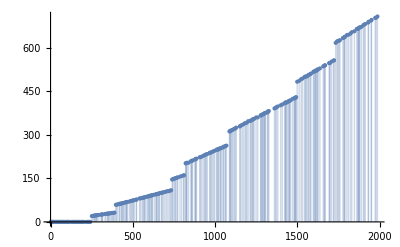

{A→1.,p→0.834028}

```mathematica
Table[{x,Sum[ChiPP[k]DivisorSum[k,inner[#,x]ChiPP[#]&,#>1&&If[PrimeQ[#],#==x,True]&&#<Power[x,0.55]/Log[Log[x]]&],{k,1,x}]},{x,Table[Prime[m],{m,1,300}]}];
ListPlot[%,Filling->Axis]
FindFit[%%,(x^p),{A,p},x]
```

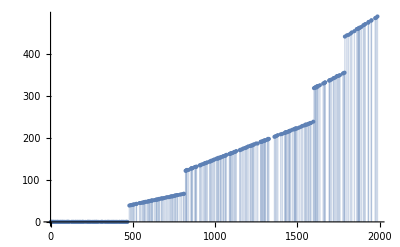

{A→1.,p→0.757907}

```mathematica
Table[{x,Sum[ChiPP[k]DivisorSum[k,inner[#,x]ChiPP[#]&,#>1&&If[PrimeQ[#],#==x,True]&&#<Power[x,0.5]/Log[Log[x]]&],{k,1,x}]},{x,Table[Prime[m],{m,1,300}]}];
ListPlot[%,Filling->Axis]
FindFit[%%,(x^p),{A,p},x]
```

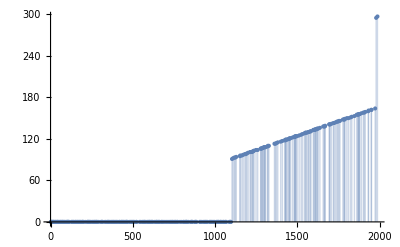

{A→1.,p→0.621422}

```mathematica
Table[{x,Sum[ChiPP[k]DivisorSum[k,inner[#,x]ChiPP[#]&,#>1&&If[PrimeQ[#],#==x,True]&&#<Power[x,0.45]/Log[Log[x]]&],{k,1,x}]},{x,Table[Prime[m],{m,1,300}]}];
ListPlot[%,Filling->Axis]
FindFit[%%,(x^p),{A,p},x]
```

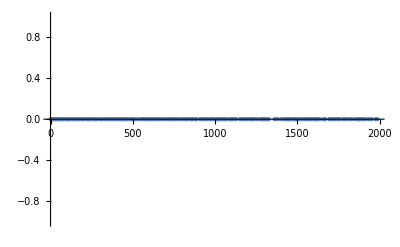

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{A→1.,p→-126.819}

```mathematica
Table[{x,Sum[ChiPP[k]DivisorSum[k,inner[#,x]ChiPP[#]&,#>1&&If[PrimeQ[#],#==x,True]&&#<Power[x,0.4]/Log[Log[x]]&],{k,1,x}]},{x,Table[Prime[m],{m,1,300}]}];
ListPlot[%,Filling->Axis]
FindFit[%%,(x^p),{A,p},x]
```

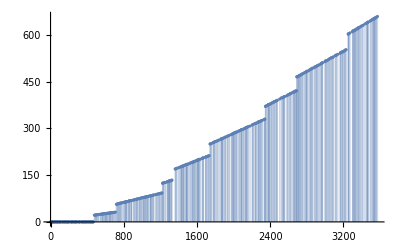

{A→1.,p→0.763648}

```mathematica
Table[{x,Sum[ChiPP[k]DivisorSum[k,inner[#,x]ChiPP[#]&,#>1&&If[PrimeQ[#],#==x,True]&&#<x^(0.45-1/Sqrt[x])&],{k,1,x}]/Log[Log[x]]},{x,Table[Prime[m],{m,1,500}]}];
ListPlot[%,Filling->Axis]
FindFit[%%,(x^p),{A,p},x]
```

Verifying Proposition 2.8:

```mathematica
Table[{Idx->x,mrange->range[x-1-N[x-2-Power[Log[Log[x]],(Pi^2)/6/Exp[EulerGamma]]],x-1-N[(x-1)(1-Exp[-1/Sqrt[x]])]],N[(x-1)Exp[-1/Sqrt[x]]],N[1+Power[Log[Log[x]],(Pi^2)/6/Exp[EulerGamma]]]},{x,2,150}] // TF
```

Idx→2 | mrange→range[0.615616+0.0941186 ⅈ,0.493069] | 0.493069 | 0.615616+0.0941186 ⅈ
Idx→3 | mrange→range[1.11267,1.12277] | 1.12277 | 1.11267
Idx→4 | mrange→range[1.3558,1.81959] | 1.81959 | 1.3558
Idx→5 | mrange→range[1.50368,2.55763] | 2.55763 | 1.50368
Idx→6 | mrange→range[1.60774,3.32407] | 3.32407 | 1.60774
Idx→7 | mrange→range[1.68676,4.11153] | 4.11153 | 1.68676
Idx→8 | mrange→range[1.74976,4.91532] | 4.91532 | 1.74976
Idx→9 | mrange→range[1.80172,5.73225] | 5.73225 | 1.80172
Idx→10 | mrange→range[1.84568,6.56004] | 6.56004 | 1.84568
Idx→11 | mrange→range[1.8836,7.39699] | 7.39699 | 1.8836
Idx→12 | mrange→range[1.9168,8.24181] | 8.24181 | 1.9168
Idx→13 | mrange→range[1.94626,9.09347] | 9.09347 | 1.94626
Idx→14 | mrange→range[1.97265,9.95115] | 9.95115 | 1.97265
Idx→15 | mrange→range[1.99652,10.8142] | 10.8142 | 1.99652
Idx→16 | mrange→range[2.01826,11.682] | 11.682 | 2.01826
Idx→17 | mrange→range[2.03819,12.5542] | 12.5542 | 2.03819
Idx→18 | mrange→range[2.05656,13.4303] | 13.4303 | 2.05656
Idx→19 | mrange→range[2.07359,14.31] | 14.31 | 2.07359
Idx→20 | mrange→range[2.08944,15.193] | 15.193 | 2.08944
Idx→21 | mrange→range[2.10424,16.079] | 16.079 | 2.10424
Idx→22 | mrange→range[2.11813,16.9679] | 16.9679 | 2.11813
Idx→23 | mrange→range[2.13119,17.8594] | 17.8594 | 2.13119
Idx→24 | mrange→range[2.14351,18.7533] | 18.7533 | 2.14351
Idx→25 | mrange→range[2.15516,19.6495] | 19.6495 | 2.15516
Idx→26 | mrange→range[2.16621,20.5479] | 20.5479 | 2.16621
Idx→27 | mrange→range[2.17671,21.4483] | 21.4483 | 2.17671
Idx→28 | mrange→range[2.1867,22.3506] | 22.3506 | 2.1867
Idx→29 | mrange→range[2.19624,23.2547] | 23.2547 | 2.19624
Idx→30 | mrange→range[2.20535,24.1606] | 24.1606 | 2.20535
Idx→31 | mrange→range[2.21407,25.068] | 25.068 | 2.21407
Idx→32 | mrange→range[2.22244,25.977] | 25.977 | 2.22244
Idx→33 | mrange→range[2.23046,26.8874] | 26.8874 | 2.23046
Idx→34 | mrange→range[2.23818,27.7992] | 27.7992 | 2.23818
Idx→35 | mrange→range[2.24561,28.7124] | 28.7124 | 2.24561
Idx→36 | mrange→range[2.25276,29.6269] | 29.6269 | 2.25276
Idx→37 | mrange→range[2.25966,30.5425] | 30.5425 | 2.25966
Idx→38 | mrange→range[2.26633,31.4594] | 31.4594 | 2.26633
Idx→39 | mrange→range[2.27277,32.3773] | 32.3773 | 2.27277
Idx→40 | mrange→range[2.27901,33.2963] | 33.2963 | 2.27901
Idx→41 | mrange→range[2.28504,34.2164] | 34.2164 | 2.28504
Idx→42 | mrange→range[2.29089,35.1375] | 35.1375 | 2.29089
Idx→43 | mrange→range[2.29657,36.0595] | 36.0595 | 2.29657
Idx→44 | mrange→range[2.30207,36.9825] | 36.9825 | 2.30207
Idx→45 | mrange→range[2.30742,37.9063] | 37.9063 | 2.30742
Idx→46 | mrange→range[2.31262,38.8311] | 38.8311 | 2.31262
Idx→47 | mrange→range[2.31768,39.7566] | 39.7566 | 2.31768
Idx→48 | mrange→range[2.3226,40.683] | 40.683 | 2.3226
Idx→49 | mrange→range[2.3274,41.6101] | 41.6101 | 2.3274
Idx→50 | mrange→range[2.33207,42.538] | 42.538 | 2.33207
Idx→51 | mrange→range[2.33662,43.4667] | 43.4667 | 2.33662
Idx→52 | mrange→range[2.34106,44.3961] | 44.3961 | 2.34106
Idx→53 | mrange→range[2.3454,45.3261] | 45.3261 | 2.3454
Idx→54 | mrange→range[2.34963,46.2568] | 46.2568 | 2.34963
Idx→55 | mrange→range[2.35376,47.1882] | 47.1882 | 2.35376
Idx→56 | mrange→range[2.3578,48.1202] | 48.1202 | 2.3578
Idx→57 | mrange→range[2.36175,49.0529] | 49.0529 | 2.36175
Idx→58 | mrange→range[2.36562,49.9861] | 49.9861 | 2.36562
Idx→59 | mrange→range[2.3694,50.9199] | 50.9199 | 2.3694
Idx→60 | mrange→range[2.3731,51.8543] | 51.8543 | 2.3731
Idx→61 | mrange→range[2.37672,52.7893] | 52.7893 | 2.37672
Idx→62 | mrange→range[2.38027,53.7247] | 53.7247 | 2.38027
Idx→63 | mrange→range[2.38375,54.6608] | 54.6608 | 2.38375
Idx→64 | mrange→range[2.38716,55.5973] | 55.5973 | 2.38716
Idx→65 | mrange→range[2.39051,56.5343] | 56.5343 | 2.39051
Idx→66 | mrange→range[2.39379,57.4719] | 57.4719 | 2.39379
Idx→67 | mrange→range[2.39701,58.4099] | 58.4099 | 2.39701
Idx→68 | mrange→range[2.40017,59.3484] | 59.3484 | 2.40017
Idx→69 | mrange→range[2.40327,60.2873] | 60.2873 | 2.40327
Idx→70 | mrange→range[2.40631,61.2267] | 61.2267 | 2.40631
Idx→71 | mrange→range[2.40931,62.1666] | 62.1666 | 2.40931
Idx→72 | mrange→range[2.41225,63.1068] | 63.1068 | 2.41225
Idx→73 | mrange→range[2.41514,64.0475] | 64.0475 | 2.41514
Idx→74 | mrange→range[2.41798,64.9886] | 64.9886 | 2.41798
Idx→75 | mrange→range[2.42077,65.9301] | 65.9301 | 2.42077
Idx→76 | mrange→range[2.42352,66.872] | 66.872 | 2.42352
Idx→77 | mrange→range[2.42622,67.8143] | 67.8143 | 2.42622
Idx→78 | mrange→range[2.42888,68.7569] | 68.7569 | 2.42888
Idx→79 | mrange→range[2.4315,69.7] | 69.7 | 2.4315
Idx→80 | mrange→range[2.43408,70.6434] | 70.6434 | 2.43408
Idx→81 | mrange→range[2.43661,71.5871] | 71.5871 | 2.43661
Idx→82 | mrange→range[2.43911,72.5313] | 72.5313 | 2.43911
Idx→83 | mrange→range[2.44158,73.4757] | 73.4757 | 2.44158
Idx→84 | mrange→range[2.444,74.4205] | 74.4205 | 2.444
Idx→85 | mrange→range[2.44639,75.3656] | 75.3656 | 2.44639
Idx→86 | mrange→range[2.44874,76.3111] | 76.3111 | 2.44874
Idx→87 | mrange→range[2.45107,77.2569] | 77.2569 | 2.45107
Idx→88 | mrange→range[2.45335,78.203] | 78.203 | 2.45335
Idx→89 | mrange→range[2.45561,79.1494] | 79.1494 | 2.45561
Idx→90 | mrange→range[2.45784,80.0961] | 80.0961 | 2.45784
Idx→91 | mrange→range[2.46003,81.0431] | 81.0431 | 2.46003
Idx→92 | mrange→range[2.4622,81.9904] | 81.9904 | 2.4622
Idx→93 | mrange→range[2.46434,82.938] | 82.938 | 2.46434
Idx→94 | mrange→range[2.46644,83.8859] | 83.8859 | 2.46644
Idx→95 | mrange→range[2.46853,84.834] | 84.834 | 2.46853
Idx→96 | mrange→range[2.47058,85.7825] | 85.7825 | 2.47058
Idx→97 | mrange→range[2.47261,86.7312] | 86.7312 | 2.47261
Idx→98 | mrange→range[2.47461,87.6802] | 87.6802 | 2.47461
Idx→99 | mrange→range[2.47659,88.6294] | 88.6294 | 2.47659
Idx→100 | mrange→range[2.47854,89.5789] | 89.5789 | 2.47854
Idx→101 | mrange→range[2.48047,90.5287] | 90.5287 | 2.48047
Idx→102 | mrange→range[2.48238,91.4787] | 91.4787 | 2.48238
Idx→103 | mrange→range[2.48426,92.4289] | 92.4289 | 2.48426
Idx→104 | mrange→range[2.48613,93.3794] | 93.3794 | 2.48613
Idx→105 | mrange→range[2.48796,94.3302] | 94.3302 | 2.48796
Idx→106 | mrange→range[2.48978,95.2811] | 95.2811 | 2.48978
Idx→107 | mrange→range[2.49158,96.2323] | 96.2323 | 2.49158
Idx→108 | mrange→range[2.49336,97.1838] | 97.1838 | 2.49336
Idx→109 | mrange→range[2.49511,98.1354] | 98.1354 | 2.49511
Idx→110 | mrange→range[2.49685,99.0873] | 99.0873 | 2.49685
Idx→111 | mrange→range[2.49857,100.039] | 100.039 | 2.49857
Idx→112 | mrange→range[2.50027,100.992] | 100.992 | 2.50027
Idx→113 | mrange→range[2.50195,101.944] | 101.944 | 2.50195
Idx→114 | mrange→range[2.50361,102.897] | 102.897 | 2.50361
Idx→115 | mrange→range[2.50526,103.85] | 103.85 | 2.50526
Idx→116 | mrange→range[2.50688,104.803] | 104.803 | 2.50688
Idx→117 | mrange→range[2.5085,105.757] | 105.757 | 2.5085
Idx→118 | mrange→range[2.51009,106.71] | 106.71 | 2.51009
Idx→119 | mrange→range[2.51167,107.664] | 107.664 | 2.51167
Idx→120 | mrange→range[2.51323,108.618] | 108.618 | 2.51323
Idx→121 | mrange→range[2.51477,109.572] | 109.572 | 2.51477
Idx→122 | mrange→range[2.5163,110.526] | 110.526 | 2.5163
Idx→123 | mrange→range[2.51782,111.481] | 111.481 | 2.51782
Idx→124 | mrange→range[2.51932,112.436] | 112.436 | 2.51932
Idx→125 | mrange→range[2.5208,113.391] | 113.391 | 2.5208
Idx→126 | mrange→range[2.52227,114.346] | 114.346 | 2.52227
Idx→127 | mrange→range[2.52373,115.301] | 115.301 | 2.52373
Idx→128 | mrange→range[2.52517,116.256] | 116.256 | 2.52517
Idx→129 | mrange→range[2.5266,117.212] | 117.212 | 2.5266
Idx→130 | mrange→range[2.52802,118.168] | 118.168 | 2.52802
Idx→131 | mrange→range[2.52942,119.124] | 119.124 | 2.52942
Idx→132 | mrange→range[2.53081,120.08] | 120.08 | 2.53081
Idx→133 | mrange→range[2.53219,121.036] | 121.036 | 2.53219
Idx→134 | mrange→range[2.53355,121.993] | 121.993 | 2.53355
Idx→135 | mrange→range[2.53491,122.949] | 122.949 | 2.53491
Idx→136 | mrange→range[2.53625,123.906] | 123.906 | 2.53625
Idx→137 | mrange→range[2.53757,124.863] | 124.863 | 2.53757
Idx→138 | mrange→range[2.53889,125.82] | 125.82 | 2.53889
Idx→139 | mrange→range[2.54019,126.778] | 126.778 | 2.54019
Idx→140 | mrange→range[2.54149,127.735] | 127.735 | 2.54149
Idx→141 | mrange→range[2.54277,128.693] | 128.693 | 2.54277
Idx→142 | mrange→range[2.54404,129.65] | 129.65 | 2.54404
Idx→143 | mrange→range[2.5453,130.608] | 130.608 | 2.5453
Idx→144 | mrange→range[2.54655,131.566] | 131.566 | 2.54655
Idx→145 | mrange→range[2.54779,132.525] | 132.525 | 2.54779
Idx→146 | mrange→range[2.54902,133.483] | 133.483 | 2.54902
Idx→147 | mrange→range[2.55024,134.441] | 134.441 | 2.55024
Idx→148 | mrange→range[2.55145,135.4] | 135.4 | 2.55145
Idx→149 | mrange→range[2.55265,136.359] | 136.359 | 2.55265
Idx→150 | mrange→range[2.55384,137.318] | 137.318 | 2.55384

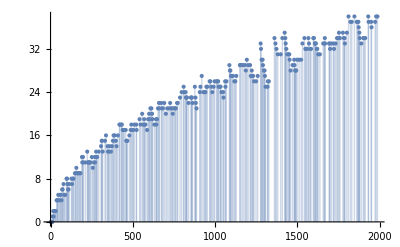

{p→0.46931}

```mathematica
inner[d_,x_]:=DivisorSum[GCD[d,x],#&]
pts=Table[{x,Sum[ChiPP[k]DivisorSum[k,inner[#,x]ChiPP[#]&,#≥Floor[(x-1)Exp[-1/Sqrt[x]]]&],{k,1,x}]},{x,Table[Prime[m],{m,1,300}]}];
ListPlot[%,Filling->Axis]
FindFit[%%,x^p,{p},x]
```

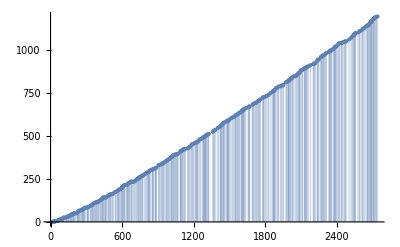

{A→1.,p→0.882814}

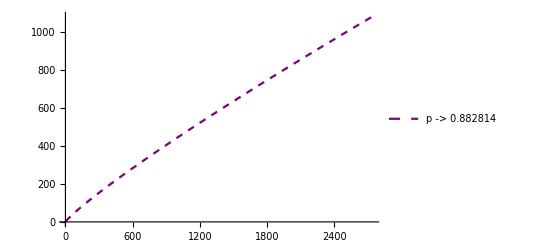

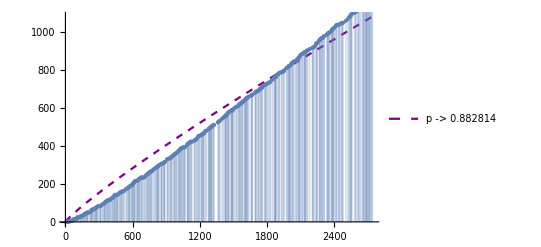

```mathematica
(****: T function : ****)
inner2[d_,x_]:=DivisorSum[GCD[d,x],# MoebiusMu[d/#]&]
d=Table[{x,Sum[ChiPP[k]DivisorSum[k,inner2[#,x]ChiPP[#]&,#<Floor[(x-1)Exp[-1/Sqrt[x]]]&],{k,1,x}]},{x,Table[Prime[m],{m,4,400}]}];
ListPlot[%,Filling->Axis]
FindFit[d,(x^p),{A,p},x]
pval=p/.%;
Plot[x^pval,{x,2,Prime[400]},PlotStyle->{Dashed,Purple},PlotLegends->Placed[{ToString[%%[[2]]]},Above]]
Show[%,%%%%]
```

Proposition 2.9:

```mathematica
eps[p_,n_]:=With[{pexp=Select[FactorInteger[n],#[[1]]==p&]},If[pexp≠{},pexp[[1]][[2]],0]]
PI[x_]:=If[PrimeQ[x],1,0]
S1[alpha_,x_]:=Sum[PI[p](p^(alpha*k))HarmonicNumber[Floor[x/(p^k)],1-alpha](Floor[x/(p^k)]-Floor[x/(p^k)-1/p]-1/p),{p,2,x},{k,1,eps[p,x]+1}]
S2[alpha_,x_]:=Sum[PI[p]Power[2,alpha-1]Power[p,alpha*k]Power[-1,Floor[x/Power[p,k-1]]]HarmonicNumber[Floor[x/2/Power[p,k]],1-alpha](Floor[x/Power[p,k]]-Floor[x/Power[p,k]-1/p]-1/p),{p,3,x},{k,1,eps[p,x]+1}]

S1CheckFormula1[q_,r_]:=Sum[PI[p]If[p==q,0,1]p HarmonicNumber[Floor[(q^r)/p],0](Floor[(q^r)/p]-Floor[(q^r)/p-1/p]-1/p),{p,2,q^r}]+Sum[Power[q,k]Floor[Power[q,r-k]](Floor[Power[q,r-k]]-Floor[Power[q,r-k]-1/q]-1/q),{k,1,r+1}]

S1CheckFormula2[q_,r_]:=Sum[-PI[p]If[p==q,0,1]((q^r)/p-FractionalPart[(q^r)/p]),{p,2,q^r-1}]+Sum[Power[q,r](1-1/q),{k,1,r}]
```

```mathematica
Table[idx[q,r]->{Floor[(q^r)/p],Floor[(q^r)/p-1/p],Floor[(q^r)/p]-Floor[(q^r)/p-1/p]},{q,Table[Prime[m],{m,1,15}]},{r,1,4},{p,Select[Table[Prime[m],{m,1,15}],#<q&]}] // TF
```

|  |  | 
idx[3,1]→{1,1,0} | idx[3,2]→{4,4,0} | idx[3,3]→{13,13,0} | idx[3,4]→{40,40,0}
idx[5,1]→{2,2,0}
idx[5,1]→{1,1,0} | idx[5,2]→{12,12,0}
idx[5,2]→{8,8,0} | idx[5,3]→{62,62,0}
idx[5,3]→{41,41,0} | idx[5,4]→{312,312,0}
idx[5,4]→{208,208,0}
idx[7,1]→{3,3,0}
idx[7,1]→{2,2,0}
idx[7,1]→{1,1,0} | idx[7,2]→{24,24,0}
idx[7,2]→{16,16,0}
idx[7,2]→{9,9,0} | idx[7,3]→{171,171,0}
idx[7,3]→{114,114,0}
idx[7,3]→{68,68,0} | idx[7,4]→{1200,1200,0}
idx[7,4]→{800,800,0}
idx[7,4]→{480,480,0}
idx[11,1]→{5,5,0}
idx[11,1]→{3,3,0}
idx[11,1]→{2,2,0}
idx[11,1]→{1,1,0} | idx[11,2]→{60,60,0}
idx[11,2]→{40,40,0}
idx[11,2]→{24,24,0}
idx[11,2]→{17,17,0} | idx[11,3]→{665,665,0}
idx[11,3]→{443,443,0}
idx[11,3]→{266,266,0}
idx[11,3]→{190,190,0} | idx[11,4]→{7320,7320,0}
idx[11,4]→{4880,4880,0}
idx[11,4]→{2928,2928,0}
idx[11,4]→{2091,2091,0}
idx[13,1]→{6,6,0}
idx[13,1]→{4,4,0}
idx[13,1]→{2,2,0}
idx[13,1]→{1,1,0}
idx[13,1]→{1,1,0} | idx[13,2]→{84,84,0}
idx[13,2]→{56,56,0}
idx[13,2]→{33,33,0}
idx[13,2]→{24,24,0}
idx[13,2]→{15,15,0} | idx[13,3]→{1098,1098,0}
idx[13,3]→{732,732,0}
idx[13,3]→{439,439,0}
idx[13,3]→{313,313,0}
idx[13,3]→{199,199,0} | idx[13,4]→{14280,14280,0}
idx[13,4]→{9520,9520,0}
idx[13,4]→{5712,5712,0}
idx[13,4]→{4080,4080,0}
idx[13,4]→{2596,2596,0}
idx[17,1]→{8,8,0}
idx[17,1]→{5,5,0}
idx[17,1]→{3,3,0}
idx[17,1]→{2,2,0}
idx[17,1]→{1,1,0}
idx[17,1]→{1,1,0} | idx[17,2]→{144,144,0}
idx[17,2]→{96,96,0}
idx[17,2]→{57,57,0}
idx[17,2]→{41,41,0}
idx[17,2]→{26,26,0}
idx[17,2]→{22,22,0} | idx[17,3]→{2456,2456,0}
idx[17,3]→{1637,1637,0}
idx[17,3]→{982,982,0}
idx[17,3]→{701,701,0}
idx[17,3]→{446,446,0}
idx[17,3]→{377,377,0} | idx[17,4]→{41760,41760,0}
idx[17,4]→{27840,27840,0}
idx[17,4]→{16704,16704,0}
idx[17,4]→{11931,11931,0}
idx[17,4]→{7592,7592,0}
idx[17,4]→{6424,6424,0}
idx[19,1]→{9,9,0}
idx[19,1]→{6,6,0}
idx[19,1]→{3,3,0}
idx[19,1]→{2,2,0}
idx[19,1]→{1,1,0}
idx[19,1]→{1,1,0}
idx[19,1]→{1,1,0} | idx[19,2]→{180,180,0}
idx[19,2]→{120,120,0}
idx[19,2]→{72,72,0}
idx[19,2]→{51,51,0}
idx[19,2]→{32,32,0}
idx[19,2]→{27,27,0}
idx[19,2]→{21,21,0} | idx[19,3]→{3429,3429,0}
idx[19,3]→{2286,2286,0}
idx[19,3]→{1371,1371,0}
idx[19,3]→{979,979,0}
idx[19,3]→{623,623,0}
idx[19,3]→{527,527,0}
idx[19,3]→{403,403,0} | idx[19,4]→{65160,65160,0}
idx[19,4]→{43440,43440,0}
idx[19,4]→{26064,26064,0}
idx[19,4]→{18617,18617,0}
idx[19,4]→{11847,11847,0}
idx[19,4]→{10024,10024,0}
idx[19,4]→{7665,7665,0}
idx[23,1]→{11,11,0}
idx[23,1]→{7,7,0}
idx[23,1]→{4,4,0}
idx[23,1]→{3,3,0}
idx[23,1]→{2,2,0}
idx[23,1]→{1,1,0}
idx[23,1]→{1,1,0}
idx[23,1]→{1,1,0} | idx[23,2]→{264,264,0}
idx[23,2]→{176,176,0}
idx[23,2]→{105,105,0}
idx[23,2]→{75,75,0}
idx[23,2]→{48,48,0}
idx[23,2]→{40,40,0}
idx[23,2]→{31,31,0}
idx[23,2]→{27,27,0} | idx[23,3]→{6083,6083,0}
idx[23,3]→{4055,4055,0}
idx[23,3]→{2433,2433,0}
idx[23,3]→{1738,1738,0}
idx[23,3]→{1106,1106,0}
idx[23,3]→{935,935,0}
idx[23,3]→{715,715,0}
idx[23,3]→{640,640,0} | idx[23,4]→{139920,139920,0}
idx[23,4]→{93280,93280,0}
idx[23,4]→{55968,55968,0}
idx[23,4]→{39977,39977,0}
idx[23,4]→{25440,25440,0}
idx[23,4]→{21526,21526,0}
idx[23,4]→{16461,16461,0}
idx[23,4]→{14728,14728,0}
idx[29,1]→{14,14,0}
idx[29,1]→{9,9,0}
idx[29,1]→{5,5,0}
idx[29,1]→{4,4,0}
idx[29,1]→{2,2,0}
idx[29,1]→{2,2,0}
idx[29,1]→{1,1,0}
idx[29,1]→{1,1,0}
idx[29,1]→{1,1,0} | idx[29,2]→{420,420,0}
idx[29,2]→{280,280,0}
idx[29,2]→{168,168,0}
idx[29,2]→{120,120,0}
idx[29,2]→{76,76,0}
idx[29,2]→{64,64,0}
idx[29,2]→{49,49,0}
idx[29,2]→{44,44,0}
idx[29,2]→{36,36,0} | idx[29,3]→{12194,12194,0}
idx[29,3]→{8129,8129,0}
idx[29,3]→{4877,4877,0}
idx[29,3]→{3484,3484,0}
idx[29,3]→{2217,2217,0}
idx[29,3]→{1876,1876,0}
idx[29,3]→{1434,1434,0}
idx[29,3]→{1283,1283,0}
idx[29,3]→{1060,1060,0} | idx[29,4]→{353640,353640,0}
idx[29,4]→{235760,235760,0}
idx[29,4]→{141456,141456,0}
idx[29,4]→{101040,101040,0}
idx[29,4]→{64298,64298,0}
idx[29,4]→{54406,54406,0}
idx[29,4]→{41604,41604,0}
idx[29,4]→{37225,37225,0}
idx[29,4]→{30751,30751,0}
idx[31,1]→{15,15,0}
idx[31,1]→{10,10,0}
idx[31,1]→{6,6,0}
idx[31,1]→{4,4,0}
idx[31,1]→{2,2,0}
idx[31,1]→{2,2,0}
idx[31,1]→{1,1,0}
idx[31,1]→{1,1,0}
idx[31,1]→{1,1,0}
idx[31,1]→{1,1,0} | idx[31,2]→{480,480,0}
idx[31,2]→{320,320,0}
idx[31,2]→{192,192,0}
idx[31,2]→{137,137,0}
idx[31,2]→{87,87,0}
idx[31,2]→{73,73,0}
idx[31,2]→{56,56,0}
idx[31,2]→{50,50,0}
idx[31,2]→{41,41,0}
idx[31,2]→{33,33,0} | idx[31,3]→{14895,14895,0}
idx[31,3]→{9930,9930,0}
idx[31,3]→{5958,5958,0}
idx[31,3]→{4255,4255,0}
idx[31,3]→{2708,2708,0}
idx[31,3]→{2291,2291,0}
idx[31,3]→{1752,1752,0}
idx[31,3]→{1567,1567,0}
idx[31,3]→{1295,1295,0}
idx[31,3]→{1027,1027,0} | idx[31,4]→{461760,461760,0}
idx[31,4]→{307840,307840,0}
idx[31,4]→{184704,184704,0}
idx[31,4]→{131931,131931,0}
idx[31,4]→{83956,83956,0}
idx[31,4]→{71040,71040,0}
idx[31,4]→{54324,54324,0}
idx[31,4]→{48606,48606,0}
idx[31,4]→{40153,40153,0}
idx[31,4]→{31845,31845,0}
idx[37,1]→{18,18,0}
idx[37,1]→{12,12,0}
idx[37,1]→{7,7,0}
idx[37,1]→{5,5,0}
idx[37,1]→{3,3,0}
idx[37,1]→{2,2,0}
idx[37,1]→{2,2,0}
idx[37,1]→{1,1,0}
idx[37,1]→{1,1,0}
idx[37,1]→{1,1,0}
idx[37,1]→{1,1,0} | idx[37,2]→{684,684,0}
idx[37,2]→{456,456,0}
idx[37,2]→{273,273,0}
idx[37,2]→{195,195,0}
idx[37,2]→{124,124,0}
idx[37,2]→{105,105,0}
idx[37,2]→{80,80,0}
idx[37,2]→{72,72,0}
idx[37,2]→{59,59,0}
idx[37,2]→{47,47,0}
idx[37,2]→{44,44,0} | idx[37,3]→{25326,25326,0}
idx[37,3]→{16884,16884,0}
idx[37,3]→{10130,10130,0}
idx[37,3]→{7236,7236,0}
idx[37,3]→{4604,4604,0}
idx[37,3]→{3896,3896,0}
idx[37,3]→{2979,2979,0}
idx[37,3]→{2665,2665,0}
idx[37,3]→{2202,2202,0}
idx[37,3]→{1746,1746,0}
idx[37,3]→{1633,1633,0} | idx[37,4]→{937080,937080,0}
idx[37,4]→{624720,624720,0}
idx[37,4]→{374832,374832,0}
idx[37,4]→{267737,267737,0}
idx[37,4]→{170378,170378,0}
idx[37,4]→{144166,144166,0}
idx[37,4]→{110244,110244,0}
idx[37,4]→{98640,98640,0}
idx[37,4]→{81485,81485,0}
idx[37,4]→{64626,64626,0}
idx[37,4]→{60456,60456,0}
idx[41,1]→{20,20,0}
idx[41,1]→{13,13,0}
idx[41,1]→{8,8,0}
idx[41,1]→{5,5,0}
idx[41,1]→{3,3,0}
idx[41,1]→{3,3,0}
idx[41,1]→{2,2,0}
idx[41,1]→{2,2,0}
idx[41,1]→{1,1,0}
idx[41,1]→{1,1,0}
idx[41,1]→{1,1,0}
idx[41,1]→{1,1,0} | idx[41,2]→{840,840,0}
idx[41,2]→{560,560,0}
idx[41,2]→{336,336,0}
idx[41,2]→{240,240,0}
idx[41,2]→{152,152,0}
idx[41,2]→{129,129,0}
idx[41,2]→{98,98,0}
idx[41,2]→{88,88,0}
idx[41,2]→{73,73,0}
idx[41,2]→{57,57,0}
idx[41,2]→{54,54,0}
idx[41,2]→{45,45,0} | idx[41,3]→{34460,34460,0}
idx[41,3]→{22973,22973,0}
idx[41,3]→{13784,13784,0}
idx[41,3]→{9845,9845,0}
idx[41,3]→{6265,6265,0}
idx[41,3]→{5301,5301,0}
idx[41,3]→{4054,4054,0}
idx[41,3]→{3627,3627,0}
idx[41,3]→{2996,2996,0}
idx[41,3]→{2376,2376,0}
idx[41,3]→{2223,2223,0}
idx[41,3]→{1862,1862,0} | idx[41,4]→{1412880,1412880,0}
idx[41,4]→{941920,941920,0}
idx[41,4]→{565152,565152,0}
idx[41,4]→{403680,403680,0}
idx[41,4]→{256887,256887,0}
idx[41,4]→{217366,217366,0}
idx[41,4]→{166221,166221,0}
idx[41,4]→{148724,148724,0}
idx[41,4]→{122859,122859,0}
idx[41,4]→{97440,97440,0}
idx[41,4]→{91153,91153,0}
idx[41,4]→{76371,76371,0}
idx[43,1]→{21,21,0}
idx[43,1]→{14,14,0}
idx[43,1]→{8,8,0}
idx[43,1]→{6,6,0}
idx[43,1]→{3,3,0}
idx[43,1]→{3,3,0}
idx[43,1]→{2,2,0}
idx[43,1]→{2,2,0}
idx[43,1]→{1,1,0}
idx[43,1]→{1,1,0}
idx[43,1]→{1,1,0}
idx[43,1]→{1,1,0}
idx[43,1]→{1,1,0} | idx[43,2]→{924,924,0}
idx[43,2]→{616,616,0}
idx[43,2]→{369,369,0}
idx[43,2]→{264,264,0}
idx[43,2]→{168,168,0}
idx[43,2]→{142,142,0}
idx[43,2]→{108,108,0}
idx[43,2]→{97,97,0}
idx[43,2]→{80,80,0}
idx[43,2]→{63,63,0}
idx[43,2]→{59,59,0}
idx[43,2]→{49,49,0}
idx[43,2]→{45,45,0} | idx[43,3]→{39753,39753,0}
idx[43,3]→{26502,26502,0}
idx[43,3]→{15901,15901,0}
idx[43,3]→{11358,11358,0}
idx[43,3]→{7227,7227,0}
idx[43,3]→{6115,6115,0}
idx[43,3]→{4676,4676,0}
idx[43,3]→{4184,4184,0}
idx[43,3]→{3456,3456,0}
idx[43,3]→{2741,2741,0}
idx[43,3]→{2564,2564,0}
idx[43,3]→{2148,2148,0}
idx[43,3]→{1939,1939,0} | idx[43,4]→{1709400,1709400,0}
idx[43,4]→{1139600,1139600,0}
idx[43,4]→{683760,683760,0}
idx[43,4]→{488400,488400,0}
idx[43,4]→{310800,310800,0}
idx[43,4]→{262984,262984,0}
idx[43,4]→{201105,201105,0}
idx[43,4]→{179936,179936,0}
idx[43,4]→{148643,148643,0}
idx[43,4]→{117889,117889,0}
idx[43,4]→{110283,110283,0}
idx[43,4]→{92400,92400,0}
idx[43,4]→{83385,83385,0}
idx[47,1]→{23,23,0}
idx[47,1]→{15,15,0}
idx[47,1]→{9,9,0}
idx[47,1]→{6,6,0}
idx[47,1]→{4,4,0}
idx[47,1]→{3,3,0}
idx[47,1]→{2,2,0}
idx[47,1]→{2,2,0}
idx[47,1]→{2,2,0}
idx[47,1]→{1,1,0}
idx[47,1]→{1,1,0}
idx[47,1]→{1,1,0}
idx[47,1]→{1,1,0}
idx[47,1]→{1,1,0} | idx[47,2]→{1104,1104,0}
idx[47,2]→{736,736,0}
idx[47,2]→{441,441,0}
idx[47,2]→{315,315,0}
idx[47,2]→{200,200,0}
idx[47,2]→{169,169,0}
idx[47,2]→{129,129,0}
idx[47,2]→{116,116,0}
idx[47,2]→{96,96,0}
idx[47,2]→{76,76,0}
idx[47,2]→{71,71,0}
idx[47,2]→{59,59,0}
idx[47,2]→{53,53,0}
idx[47,2]→{51,51,0} | idx[47,3]→{51911,51911,0}
idx[47,3]→{34607,34607,0}
idx[47,3]→{20764,20764,0}
idx[47,3]→{14831,14831,0}
idx[47,3]→{9438,9438,0}
idx[47,3]→{7986,7986,0}
idx[47,3]→{6107,6107,0}
idx[47,3]→{5464,5464,0}
idx[47,3]→{4514,4514,0}
idx[47,3]→{3580,3580,0}
idx[47,3]→{3349,3349,0}
idx[47,3]→{2806,2806,0}
idx[47,3]→{2532,2532,0}
idx[47,3]→{2414,2414,0} | idx[47,4]→{2439840,2439840,0}
idx[47,4]→{1626560,1626560,0}
idx[47,4]→{975936,975936,0}
idx[47,4]→{697097,697097,0}
idx[47,4]→{443607,443607,0}
idx[47,4]→{375360,375360,0}
idx[47,4]→{287040,287040,0}
idx[47,4]→{256825,256825,0}
idx[47,4]→{212160,212160,0}
idx[47,4]→{168264,168264,0}
idx[47,4]→{157409,157409,0}
idx[47,4]→{131883,131883,0}
idx[47,4]→{119016,119016,0}
idx[47,4]→{113480,113480,0}

```mathematica
Table[idx[q,r]->{S1[1,q^r],S1CheckFormula1[q,r],S1CheckFormula2[q,r]},{q,Table[Prime[m],{m,1,8}]},{r,1,4}] // TF
```

idx[2,1]→{1,1,1} | idx[2,2]→{3,3,3} | idx[2,3]→{8,8,8} | idx[2,4]→{20,20,20}
idx[3,1]→{1,1,1} | idx[3,2]→{6,6,6} | idx[3,3]→{26,26,26} | idx[3,4]→{109,109,109}
idx[5,1]→{1,1,1} | idx[5,2]→{11,11,11} | idx[5,3]→{106,106,106} | idx[5,4]→{843,843,843}
idx[7,1]→{0,0,0} | idx[7,2]→{16,16,16} | idx[7,3]→{262,262,262} | idx[7,4]→{3168,3168,3168}
idx[11,1]→{-1,-1,-1} | idx[11,2]→{19,19,19} | idx[11,3]→{865,865,865} | idx[11,4]→{18368,18368,18368}
idx[13,1]→{-2,-2,-2} | idx[13,2]→{19,19,19} | idx[13,3]→{1332,1332,1332} | idx[13,4]→{35008,35008,35008}
idx[17,1]→{-4,-4,-4} | idx[17,2]→{7,7,7} | idx[17,3]→{2639,2639,2639} | idx[17,4]→{98220,98220,98220}
idx[19,1]→{-5,-5,-5} | idx[19,2]→{-3,-3,-3} | idx[19,3]→{3490,3490,3490} | idx[19,4]→{150431,150431,150431}

```mathematica
Table[{Idx->x,Abs[TauDivisorSum[0,x]],N[x*Log[Log[x]]/10],Abs[TauDivisorSum[0,x]]/N[x*Log[Log[x]]]},{x,Table[Prime[m],{m,1,150}]}] // TF
```

Idx→2 | 0 | -0.0733026 | 0.
Idx→3 | 0 | 0.0282143 | 0.
Idx→5 | 0 | 0.237942 | 0.
Idx→7 | 0 | 0.466011 | 0.
Idx→11 | 0 | 0.962051 | 0.
Idx→13 | 0 | 1.22452 | 0.
Idx→17 | 1 | 1.7704 | 0.0564844
Idx→19 | 1 | 2.05184 | 0.0487366
Idx→23 | 2 | 2.62841 | 0.0760916
Idx→29 | 2 | 3.52092 | 0.0568034
Idx→31 | 2 | 3.82454 | 0.0522939
Idx→37 | 4 | 4.75066 | 0.0841988
Idx→41 | 5 | 5.37918 | 0.092951
Idx→43 | 5 | 5.69637 | 0.0877751
Idx→47 | 6 | 6.33612 | 0.0946951
Idx→53 | 7 | 7.30785 | 0.0957874
Idx→59 | 9 | 8.29241 | 0.108533
Idx→61 | 9 | 8.62318 | 0.10437
Idx→67 | 11 | 9.62255 | 0.114315
Idx→71 | 12 | 10.2943 | 0.11657
Idx→73 | 12 | 10.6317 | 0.11287
Idx→79 | 14 | 11.6496 | 0.120175
Idx→83 | 14 | 12.3328 | 0.113519
Idx→89 | 16 | 13.3638 | 0.119727
Idx→97 | 19 | 14.7493 | 0.12882
Idx→101 | 20 | 15.4463 | 0.129481
Idx→103 | 20 | 15.7959 | 0.126616
Idx→107 | 22 | 16.4969 | 0.133359
Idx→109 | 22 | 16.8483 | 0.130577
Idx→113 | 23 | 17.5531 | 0.131031
Idx→127 | 27 | 20.0378 | 0.134745
Idx→131 | 28 | 20.7525 | 0.134923
Idx→137 | 30 | 21.8283 | 0.137436
Idx→139 | 30 | 22.1878 | 0.135209
Idx→149 | 34 | 23.9924 | 0.141712
Idx→151 | 34 | 24.3546 | 0.139604
Idx→157 | 36 | 25.4438 | 0.141488
Idx→163 | 38 | 26.5366 | 0.143198
Idx→167 | 40 | 27.2671 | 0.146697
Idx→173 | 41 | 28.3657 | 0.144541
Idx→179 | 43 | 29.4675 | 0.145923
Idx→181 | 43 | 29.8355 | 0.144124
Idx→191 | 47 | 31.6804 | 0.148357
Idx→193 | 47 | 32.0504 | 0.146644
Idx→197 | 49 | 32.7913 | 0.14943
Idx→199 | 49 | 33.1622 | 0.147759
Idx→211 | 54 | 35.3941 | 0.152568
Idx→223 | 59 | 37.6363 | 0.156764
Idx→227 | 60 | 38.3859 | 0.156307
Idx→229 | 60 | 38.7611 | 0.154794
Idx→233 | 62 | 39.5123 | 0.156913
Idx→239 | 64 | 40.641 | 0.157477
Idx→241 | 64 | 41.0177 | 0.15603
Idx→251 | 67 | 42.9051 | 0.156159
Idx→257 | 70 | 44.0403 | 0.158945
Idx→263 | 72 | 45.1777 | 0.159371
Idx→269 | 74 | 46.317 | 0.159769
Idx→271 | 74 | 46.6972 | 0.158468
Idx→277 | 77 | 47.8392 | 0.160956
Idx→281 | 78 | 48.6015 | 0.160489
Idx→283 | 78 | 48.983 | 0.159239
Idx→293 | 82 | 50.8936 | 0.161121
Idx→307 | 88 | 53.5766 | 0.164251
Idx→311 | 89 | 54.3449 | 0.163769
Idx→313 | 89 | 54.7293 | 0.162619
Idx→317 | 91 | 55.4987 | 0.163968
Idx→331 | 97 | 58.1972 | 0.166675
Idx→337 | 99 | 59.3563 | 0.166789
Idx→347 | 103 | 61.2915 | 0.168049
Idx→349 | 103 | 61.6791 | 0.166993
Idx→353 | 104 | 62.4546 | 0.166521
Idx→359 | 107 | 63.6192 | 0.168188
Idx→367 | 109 | 65.1741 | 0.167244
Idx→373 | 111 | 66.3419 | 0.167315
Idx→379 | 113 | 67.5111 | 0.16738
Idx→383 | 114 | 68.2912 | 0.166932
Idx→389 | 117 | 69.4626 | 0.168436
Idx→397 | 120 | 71.0264 | 0.168951
Idx→401 | 122 | 71.8092 | 0.169895
Idx→409 | 125 | 73.3763 | 0.170355
Idx→419 | 129 | 75.3384 | 0.171228
Idx→421 | 129 | 75.7312 | 0.170339
Idx→431 | 134 | 77.6971 | 0.172465
Idx→433 | 134 | 78.0907 | 0.171595
Idx→439 | 137 | 79.2722 | 0.172822
Idx→443 | 138 | 80.0605 | 0.17237
Idx→449 | 140 | 81.2438 | 0.172321
Idx→457 | 144 | 82.8233 | 0.173864
Idx→461 | 145 | 83.6138 | 0.173416
Idx→463 | 145 | 84.0092 | 0.1726
Idx→467 | 147 | 84.8004 | 0.173348
Idx→479 | 152 | 87.1768 | 0.174358
Idx→487 | 156 | 88.7633 | 0.175748
Idx→491 | 157 | 89.5572 | 0.175307
Idx→499 | 161 | 91.1464 | 0.176639
Idx→503 | 162 | 91.9416 | 0.176199
Idx→509 | 164 | 93.1353 | 0.176088
Idx→521 | 169 | 95.5254 | 0.176916
Idx→523 | 169 | 95.9241 | 0.176181
Idx→541 | 177 | 99.5172 | 0.177859
Idx→547 | 179 | 100.717 | 0.177726
Idx→557 | 184 | 102.718 | 0.179132
Idx→563 | 187 | 103.92 | 0.179947
Idx→569 | 189 | 105.122 | 0.179791
Idx→571 | 189 | 105.523 | 0.179107
Idx→577 | 191 | 106.727 | 0.178961
Idx→587 | 196 | 108.735 | 0.180254
Idx→593 | 198 | 109.941 | 0.180096
Idx→599 | 201 | 111.148 | 0.18084
Idx→601 | 201 | 111.55 | 0.180188
Idx→607 | 203 | 112.758 | 0.180031
Idx→613 | 206 | 113.967 | 0.180755
Idx→617 | 208 | 114.773 | 0.181227
Idx→619 | 208 | 115.176 | 0.180593
Idx→631 | 213 | 117.597 | 0.181127
Idx→641 | 217 | 119.617 | 0.181413
Idx→643 | 217 | 120.021 | 0.180802
Idx→647 | 219 | 120.83 | 0.181247
Idx→653 | 222 | 122.043 | 0.181903
Idx→659 | 224 | 123.258 | 0.181733
Idx→661 | 224 | 123.663 | 0.181138
Idx→673 | 231 | 126.094 | 0.183197
Idx→677 | 232 | 126.905 | 0.182814
Idx→683 | 234 | 128.122 | 0.182639
Idx→691 | 237 | 129.746 | 0.182665
Idx→701 | 242 | 131.777 | 0.183643
Idx→709 | 246 | 133.404 | 0.184402
Idx→719 | 251 | 135.439 | 0.185324
Idx→727 | 254 | 137.068 | 0.18531
Idx→733 | 255 | 138.29 | 0.184394
Idx→739 | 258 | 139.514 | 0.184928
Idx→743 | 260 | 140.33 | 0.185278
Idx→751 | 263 | 141.962 | 0.185261
Idx→757 | 265 | 143.187 | 0.185072
Idx→761 | 267 | 144.004 | 0.185411
Idx→769 | 271 | 145.639 | 0.186076
Idx→773 | 272 | 146.457 | 0.18572
Idx→787 | 279 | 149.322 | 0.186845
Idx→797 | 284 | 151.37 | 0.18762
Idx→809 | 290 | 153.83 | 0.18852
Idx→811 | 290 | 154.24 | 0.188019
Idx→821 | 295 | 156.292 | 0.188749
Idx→823 | 295 | 156.702 | 0.188255
Idx→827 | 297 | 157.524 | 0.188543
Idx→829 | 297 | 157.935 | 0.188053
Idx→839 | 301 | 159.989 | 0.188138
Idx→853 | 306 | 162.868 | 0.187882
Idx→857 | 308 | 163.691 | 0.188159
Idx→859 | 308 | 164.103 | 0.187687
Idx→863 | 310 | 164.927 | 0.187962

```mathematica
Table[{Idx->x,Abs[TauDivisorSum[0,x]],N[x*Log[Log[x]]/10],Abs[TauDivisorSum[0,x]]/N[x*Log[Log[x]]]},{x,Table[Prime[m],{m,151,180}]}] // TF
```

Idx→877 | 316 | 167.811 | 0.188308
Idx→881 | 317 | 168.635 | 0.18798
Idx→883 | 317 | 169.047 | 0.187521
Idx→887 | 319 | 169.872 | 0.187788
Idx→907 | 330 | 174. | 0.189655
Idx→911 | 331 | 174.826 | 0.189331
Idx→919 | 335 | 176.479 | 0.189824
Idx→929 | 339 | 178.547 | 0.189866
Idx→937 | 343 | 180.202 | 0.190342
Idx→941 | 344 | 181.03 | 0.190024
Idx→947 | 347 | 182.272 | 0.190375
Idx→953 | 349 | 183.515 | 0.190176
Idx→967 | 355 | 186.416 | 0.190434
Idx→971 | 357 | 187.245 | 0.190659
Idx→977 | 360 | 188.49 | 0.190992
Idx→983 | 362 | 189.735 | 0.190793
Idx→991 | 366 | 191.395 | 0.191227
Idx→997 | 368 | 192.641 | 0.191029
Idx→1009 | 375 | 195.135 | 0.192175
Idx→1013 | 376 | 195.966 | 0.19187
Idx→1019 | 379 | 197.214 | 0.192177
Idx→1021 | 379 | 197.63 | 0.191773
Idx→1031 | 384 | 199.71 | 0.192278
Idx→1033 | 384 | 200.127 | 0.191879
Idx→1039 | 387 | 201.376 | 0.192178
Idx→1049 | 392 | 203.458 | 0.192668
Idx→1051 | 392 | 203.875 | 0.192275
Idx→1061 | 396 | 205.959 | 0.192271
Idx→1063 | 396 | 206.376 | 0.191883
Idx→1069 | 399 | 207.627 | 0.192171

```mathematica
Table[{Idx->x,Abs[TauDivisorSum[0,x]],N[x*Log[Log[x]]/10],Abs[TauDivisorSum[0,x]]/N[x*Log[Log[x]]]},{x,Table[Prime[m],{m,181,300}]}] // TF
```

Idx→1087 | 409 | 211.383 | 0.193487
Idx→1091 | 410 | 212.219 | 0.193197
Idx→1093 | 410 | 212.636 | 0.192818
Idx→1097 | 412 | 213.472 | 0.193
Idx→1103 | 414 | 214.725 | 0.192805
Idx→1109 | 417 | 215.979 | 0.193074
Idx→1117 | 421 | 217.651 | 0.193429
Idx→1123 | 423 | 218.906 | 0.193233
Idx→1129 | 425 | 220.161 | 0.19304
Idx→1151 | 436 | 224.767 | 0.193979
Idx→1153 | 436 | 225.186 | 0.193618
Idx→1163 | 442 | 227.282 | 0.194472
Idx→1171 | 445 | 228.959 | 0.194358
Idx→1181 | 450 | 231.056 | 0.194758
Idx→1187 | 453 | 232.315 | 0.194994
Idx→1193 | 455 | 233.574 | 0.194799
Idx→1201 | 459 | 235.254 | 0.195109
Idx→1213 | 465 | 237.774 | 0.195564
Idx→1217 | 466 | 238.615 | 0.195294
Idx→1223 | 469 | 239.876 | 0.195518
Idx→1229 | 471 | 241.137 | 0.195325
Idx→1231 | 471 | 241.558 | 0.194985
Idx→1237 | 474 | 242.819 | 0.195207
Idx→1249 | 481 | 245.344 | 0.196051
Idx→1259 | 485 | 247.449 | 0.196
Idx→1277 | 495 | 251.241 | 0.197022
Idx→1279 | 495 | 251.662 | 0.196692
Idx→1283 | 497 | 252.505 | 0.196828
Idx→1289 | 500 | 253.77 | 0.197029
Idx→1291 | 500 | 254.192 | 0.196702
Idx→1297 | 503 | 255.457 | 0.196902
Idx→1301 | 504 | 256.301 | 0.196644
Idx→1303 | 504 | 256.723 | 0.196321
Idx→1307 | 506 | 257.567 | 0.196454
Idx→1319 | 513 | 260.099 | 0.197232
Idx→1321 | 513 | 260.522 | 0.196913
Idx→1327 | 515 | 261.789 | 0.196724
Idx→1361 | 532 | 268.974 | 0.197789
Idx→1367 | 536 | 270.243 | 0.19834
Idx→1373 | 537 | 271.513 | 0.197781
Idx→1381 | 540 | 273.206 | 0.197653
Idx→1399 | 549 | 277.017 | 0.198183
Idx→1409 | 554 | 279.135 | 0.19847
Idx→1423 | 561 | 282.103 | 0.198864
Idx→1427 | 563 | 282.951 | 0.198974
Idx→1429 | 563 | 283.375 | 0.198677
Idx→1433 | 564 | 284.223 | 0.198435
Idx→1439 | 567 | 285.496 | 0.198602
Idx→1447 | 571 | 287.194 | 0.198821
Idx→1451 | 573 | 288.043 | 0.198929
Idx→1453 | 573 | 288.467 | 0.198636
Idx→1459 | 576 | 289.741 | 0.198798
Idx→1471 | 582 | 292.289 | 0.199118
Idx→1481 | 587 | 294.414 | 0.199379
Idx→1483 | 587 | 294.839 | 0.199092
Idx→1487 | 589 | 295.689 | 0.199196
Idx→1489 | 589 | 296.114 | 0.19891
Idx→1493 | 591 | 296.964 | 0.199014
Idx→1499 | 594 | 298.24 | 0.199169
Idx→1511 | 600 | 300.792 | 0.199473
Idx→1523 | 606 | 303.345 | 0.199772
Idx→1531 | 609 | 305.048 | 0.199641
Idx→1543 | 615 | 307.603 | 0.199933
Idx→1549 | 619 | 308.881 | 0.200401
Idx→1553 | 621 | 309.734 | 0.200495
Idx→1559 | 623 | 311.012 | 0.200314
Idx→1567 | 626 | 312.717 | 0.200181
Idx→1571 | 627 | 313.57 | 0.199956
Idx→1579 | 631 | 315.275 | 0.200142
Idx→1583 | 633 | 316.128 | 0.200235
Idx→1597 | 640 | 319.115 | 0.200555
Idx→1601 | 642 | 319.969 | 0.200645
Idx→1607 | 645 | 321.249 | 0.200779
Idx→1609 | 645 | 321.676 | 0.200512
Idx→1613 | 646 | 322.53 | 0.200291
Idx→1619 | 650 | 323.811 | 0.200734
Idx→1621 | 650 | 324.238 | 0.20047
Idx→1627 | 652 | 325.52 | 0.200295
Idx→1637 | 657 | 327.656 | 0.200515
Idx→1657 | 668 | 331.931 | 0.201247
Idx→1663 | 671 | 333.214 | 0.201372
Idx→1667 | 673 | 334.069 | 0.201455
Idx→1669 | 673 | 334.497 | 0.201198
Idx→1693 | 685 | 339.633 | 0.201689
Idx→1697 | 687 | 340.489 | 0.201769
Idx→1699 | 687 | 340.917 | 0.201515
Idx→1709 | 692 | 343.058 | 0.201715
Idx→1721 | 697 | 345.629 | 0.201661
Idx→1723 | 697 | 346.057 | 0.201412
Idx→1733 | 703 | 348.2 | 0.201895
Idx→1741 | 706 | 349.915 | 0.201763
Idx→1747 | 709 | 351.202 | 0.201878
Idx→1753 | 712 | 352.488 | 0.201992
Idx→1759 | 715 | 353.775 | 0.202106
Idx→1777 | 725 | 357.637 | 0.202719
Idx→1783 | 727 | 358.925 | 0.202549
Idx→1787 | 730 | 359.784 | 0.2029
Idx→1789 | 730 | 360.213 | 0.202658
Idx→1801 | 735 | 362.79 | 0.202596
Idx→1811 | 739 | 364.938 | 0.2025
Idx→1823 | 745 | 367.517 | 0.202712
Idx→1831 | 749 | 369.237 | 0.202851
Idx→1847 | 758 | 372.677 | 0.203393
Idx→1861 | 764 | 375.688 | 0.20336
Idx→1867 | 766 | 376.979 | 0.203194
Idx→1871 | 768 | 377.84 | 0.20326
Idx→1873 | 768 | 378.271 | 0.203029
Idx→1877 | 769 | 379.132 | 0.202832
Idx→1879 | 769 | 379.562 | 0.202602
Idx→1889 | 776 | 381.715 | 0.203293
Idx→1901 | 781 | 384.3 | 0.203227
Idx→1907 | 784 | 385.592 | 0.203324
Idx→1913 | 787 | 386.885 | 0.20342
Idx→1931 | 796 | 390.764 | 0.203703
Idx→1933 | 796 | 391.196 | 0.203479
Idx→1949 | 805 | 394.646 | 0.20398
Idx→1951 | 805 | 395.077 | 0.203758
Idx→1973 | 818 | 399.824 | 0.20459
Idx→1979 | 820 | 401.119 | 0.204428
Idx→1987 | 823 | 402.846 | 0.204296

## §2.3: The complete proof of Theorem 2.1

## §2.4: Generalizations